## Set your path to NonLinearSolver and get it

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
1
```

1

### DataToEquations and the critical congestion solver

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1}, {7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9}, {7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e = Data2Equations[Data/.{I1->52,I2->104,U1->0,U2->0, U3->0}];
crit=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

It took 1.06572 seconds to preprocess.

Iterative DNF convertion took 3.99098 seconds to terminate.

Reducing took 0.18554 seconds to terminate.

Iterative DNF convertion took 0.006717 seconds to terminate.

Reducing took 0.004096 seconds to terminate.

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{5.61183,Null}

```mathematica
CriticalCongestionReduce[d2e]//AbsoluteTiming
```

It took 0.812442 seconds to preprocess.

Reducing jt10≥0&&jt11≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥208+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&364+8 jt10+jt19+jt29+jt30+u1≤9 jt17+9 jt18+jt22+jt34+jt37&&43 jt17+43 jt18+jt19+jt29+jt30+u1≤3328+44 jt10+jt22+jt34+jt37&&3276+52 jt10+3 jt22+3 jt34+3 jt37+u1≤49 jt17+49 jt18+3 (jt19+jt29+jt30)&&jt11≤104&&jt19+jt32≤jt10+jt22&&4 jt17+4 jt18+jt41+jt42≤364+4 jt10+jt27+jt28&&jt11+jt16≤jt17+jt18&&jt17+jt18≤52+jt11+jt16&&jt27≤jt16&&jt16≤jt17+jt22+jt27&&208+3 jt10+jt19≤4 jt17+3 jt18+jt22&&208+3 jt10+jt28≤4 jt17+3 jt18+jt22&&5 jt17+4 jt18+jt22≤364+4 jt10+jt16+jt28&&jt17+jt18≤156+jt10+jt16&&11 jt17+11 jt18+jt44+jt45≤780+11 jt10+jt32+jt33+jt34&&jt44+jt47≤jt27+jt28&&jt41+jt48≤jt32+jt33+jt34&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt17+33 jt18+2 (jt19+jt29+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48≤22 jt17+22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33&&(35 jt10+2 (1170+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||3276+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30))&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(2704+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||3328+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(208+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||364+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(364+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt33==0||780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==780+11 jt10+jt32+jt33+jt34)&&(jt10+jt22==jt19||208+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(364+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(208+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt27+jt28==0||4 (jt17+jt18)==364+4 jt10+jt27+jt28)&&(208+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(208+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt11+jt16==0||52+jt10+jt11+jt16==jt17+jt18)&&(52+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||156+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0) ...

Iterative DNF convertion...

... took 5.84058 seconds to terminate. 
Removing duplicates and reducing...

... took 0.010532 seconds to terminate.

Iterative DNF convertion...

... took 0.00417 seconds to terminate. 
Removing duplicates and reducing...

... took 0.002711 seconds to terminate.

Iterative DNF convertion...

... took 6.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000177 seconds to terminate.

Iterative DNF convertion...

... took 5.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000151 seconds to terminate.

Iterative DNF convertion...

... took 4.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000142 seconds to terminate.

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{6.78183,Null}

Iterative DNF convertion took 5.97392 seconds to terminate

Iterative DNF convertion took 0.109029 seconds to terminate

Iterative DNF convertion took 0.011164 seconds to terminate

Iterative DNF convertion took 0.008277 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{7.00537,Null}

Iterative DNF convertion took 6.05701 seconds to terminate

Iterative DNF convertion took 0.100968 seconds to terminate

Iterative DNF convertion took 0.010943 seconds to terminate

Iterative DNF convertion took 0.00805 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{7.07742,Null}

Iterative DNF convertion took 5.50677 seconds to terminate

Iterative DNF convertion took 0.103426 seconds to terminate

Iterative DNF convertion took 0.010735 seconds to terminate

Iterative DNF convertion took 0.00777 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{6.51655,Null}

Iterative DNF convertion took 6.0341 seconds to terminate

Iterative DNF convertion took 0.101598 seconds to terminate

Iterative DNF convertion took 0.010431 seconds to terminate

Iterative DNF convertion took 0.007378 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{7.03821,Null}

Iterative DNF convertion took 8.55197 seconds to terminate

Iterative DNF convertion took 0.120352 seconds to terminate

Iterative DNF convertion took 0.013192 seconds to terminate

Iterative DNF convertion took 0.009059 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{9.5936,Null}

Iterative DNF convertion took 7.67921 seconds to terminate

Iterative DNF convertion took 0.18949 seconds to terminate

Iterative DNF convertion took 0.026459 seconds to terminate

Iterative DNF convertion took 0.008881 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{8.80256,Null}

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-5.68434×10^-14,-1.13687×10^-13,2.13163×10^-14,-8.52651×10^-14,-9.9476×10^-14,5.32907×10^-15,-8.52651×10^-14,-8.52651×10^-14,1.11022×10^-15,-2.13163×10^-14,-6.39488×10^-14,-2.13163×10^-14,-6.39488×10^-14,-4.26326×10^-14}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-13

<|u1→257.,u2→205.,u3→328.,u4→224.,u5→205.,u6→224.,u7→205.,u8→134.,u9→224.,u10→139.,u11→134.,u12→139.,u13→134.,u14→58.,u15→139.,u16→59.,u17→58.,u18→59.,u19→58.,u20→39.,u21→58.,u22→0.,u23→59.,u24→39.,u25→59.,u26→0.,u27→39.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→257.,u36→257.,u37→328.,u38→328.,j1→0.,j2→52.,j3→0.,j4→104.,j5→19.,j6→0.,j7→0.,j8→71.,j9→0.,j10→85.,j11→5.,j12→0.,j13→0.,j14→76.,j15→0.,j16→80.,j17→1.,j18→0.,j19→0.,j20→19.,j21→0.,j22→58.,j23→0.,j24→20.,j25→0.,j26→59.,j27→0.,j28→39.,j29→0.,j30→58.,j31→0.,j32→59.,j33→0.,j34→39.,j35→0.,j36→52.,j37→0.,j38→104.,jt1→0.,jt2→52.,jt3→0.,jt4→104.,jt5→0.,jt6→52.,jt7→0.,jt8→19.,jt9→0.,jt10→0.,jt11→19.,jt12→85.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→71.,jt19→0.,jt20→5.,jt21→0.,jt22→0.,jt23→5.,jt24→80.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→18.,jt31→58.,jt32→0.,jt33→1.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→1.,jt42→20.,jt43→59.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→19.,jt55→0.,jt56→20.,jt57→0.,jt58→0.,jt59→58.,jt60→0.,jt61→59.,jt62→0.,jt63→39.,jt64→0.|>

#### Non-critical congestion solver

#### Starting from the critical congestion solution

```mathematica
Get[dddRicardo]
alpha[edge_]:=0.2
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative DNF convertion took 11.1371 seconds to terminate

Iterative DNF convertion took 0.117163 seconds to terminate

Iterative DNF convertion took 0.010788 seconds to terminate

Iterative DNF convertion took 0.006877 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 17.0303≤jt30≤17.8078

Picked one value for the variable(s) {jt30} {17.0303} (respectively)

{45.4072,95.1078,-14.7424,63.4576,76.8485,-2.64056,68.2328,72.0589,0.108731,14.7424,51.0885,15.646,52.0373,33.1792}
{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}

Max error for non-linear solution: 1.49036

Iterative DNF convertion took 11.3288 seconds to terminate

Iterative DNF convertion took 0.108405 seconds to terminate

Iterative DNF convertion took 0.015231 seconds to terminate

Iterative DNF convertion took 0.008441 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 16.0909≤jt30≤16.7337

Picked one value for the variable(s) {jt30} {16.0909} (respectively)

{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}
{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}

Max error for non-linear solution: 1.38356

Iterative DNF convertion took 10.9651 seconds to terminate

Iterative DNF convertion took 0.114088 seconds to terminate

Iterative DNF convertion took 0.011885 seconds to terminate

Iterative DNF convertion took 0.009355 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 15.1932≤jt30≤15.7633

Picked one value for the variable(s) {jt30} {15.1932} (respectively)

{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}
{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}

Max error for non-linear solution: 1.2825

Iterative DNF convertion took 11.4849 seconds to terminate

Iterative DNF convertion took 0.116271 seconds to terminate

Iterative DNF convertion took 0.017307 seconds to terminate

Iterative DNF convertion took 0.007194 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 14.3473≤jt30≤14.8831

Picked one value for the variable(s) {jt30} {14.3473} (respectively)

{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}
{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}

Max error for non-linear solution: 1.18708

Iterative DNF convertion took 11.052 seconds to terminate

Iterative DNF convertion took 0.134473 seconds to terminate

Iterative DNF convertion took 0.018144 seconds to terminate

Iterative DNF convertion took 0.009215 seconds to terminate

Iterative DNF convertion took 0.000014 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 13.5593≤jt30≤14.0822

Picked one value for the variable(s) {jt30} {13.5593} (respectively)

{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}
{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}

Max error for non-linear solution: 1.09717

Iterative DNF convertion took 11.5447 seconds to terminate

Iterative DNF convertion took 0.111107 seconds to terminate

Iterative DNF convertion took 0.013031 seconds to terminate

Iterative DNF convertion took 0.007195 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 12.8312≤jt30≤13.3524

Picked one value for the variable(s) {jt30} {12.8312} (respectively)

{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}
{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}

Max error for non-linear solution: 1.01262

Iterative DNF convertion took 11.73 seconds to terminate

Iterative DNF convertion took 0.100672 seconds to terminate

Iterative DNF convertion took 0.013234 seconds to terminate

Iterative DNF convertion took 0.00832 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 12.1624≤jt30≤12.6873

Picked one value for the variable(s) {jt30} {12.1624} (respectively)

{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}
{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}

Max error for non-linear solution: 0.933278

Iterative DNF convertion took 11.5287 seconds to terminate

Iterative DNF convertion took 0.125275 seconds to terminate

Iterative DNF convertion took 0.015408 seconds to terminate

Iterative DNF convertion took 0.008788 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 11.5506≤jt30≤12.0817

Picked one value for the variable(s) {jt30} {11.5506} (respectively)

{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}
{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}

Max error for non-linear solution: 0.858975

Iterative DNF convertion took 12.5966 seconds to terminate

Iterative DNF convertion took 0.118152 seconds to terminate

Iterative DNF convertion took 0.012684 seconds to terminate

Iterative DNF convertion took 0.007912 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.9927≤jt30≤11.5311

Picked one value for the variable(s) {jt30} {10.9927} (respectively)

{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}
{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}

Max error for non-linear solution: 0.789537

Iterative DNF convertion took 11.3249 seconds to terminate

Iterative DNF convertion took 0.12799 seconds to terminate

Iterative DNF convertion took 0.013357 seconds to terminate

Iterative DNF convertion took 0.007052 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.4852≤jt30≤11.0313

Picked one value for the variable(s) {jt30} {10.4852} (respectively)

{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}
{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}

Max error for non-linear solution: 0.724781

Iterative DNF convertion took 10.9748 seconds to terminate

Iterative DNF convertion took 0.109243 seconds to terminate

Iterative DNF convertion took 0.015662 seconds to terminate

Iterative DNF convertion took 0.009266 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.0248≤jt30≤10.5786

Picked one value for the variable(s) {jt30} {10.0248} (respectively)

{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}
{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}

Max error for non-linear solution: 0.664517

Iterative DNF convertion took 12.5463 seconds to terminate

Iterative DNF convertion took 0.11691 seconds to terminate

Iterative DNF convertion took 0.014518 seconds to terminate

Iterative DNF convertion took 0.007207 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 9.60795≤jt30≤10.1692

Picked one value for the variable(s) {jt30} {9.60795} (respectively)

{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}
{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}

Max error for non-linear solution: 0.608551

Iterative DNF convertion took 11.1132 seconds to terminate

Iterative DNF convertion took 0.124612 seconds to terminate

Iterative DNF convertion took 0.016628 seconds to terminate

Iterative DNF convertion took 0.009451 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 9.23134≤jt30≤9.79959

Picked one value for the variable(s) {jt30} {9.23134} (respectively)

{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}
{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}

Max error for non-linear solution: 0.556681

Iterative DNF convertion took 11.375 seconds to terminate

Iterative DNF convertion took 0.116888 seconds to terminate

Iterative DNF convertion took 0.014767 seconds to terminate

Iterative DNF convertion took 0.007642 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8.89177≤jt30≤9.46662

Picked one value for the variable(s) {jt30} {8.89177} (respectively)

{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}
{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}

Max error for non-linear solution: 0.508702

Iterative DNF convertion took 11.0086 seconds to terminate

Iterative DNF convertion took 0.109171 seconds to terminate

Iterative DNF convertion took 0.015896 seconds to terminate

Iterative DNF convertion took 0.007361 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8.58617≤jt30≤9.16714

Picked one value for the variable(s) {jt30} {8.58617} (respectively)

{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}

Max error for non-linear solution: 0.464406

Iterated 15 times out of 15

{187.336,Null}

All restrictions are True

Nlhs: {45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.464406

Iterative DNF convertion took 13.6054 seconds to terminate

Iterative DNF convertion took 0.064656 seconds to terminate

Iterative DNF convertion took 0.008541 seconds to terminate

Iterative DNF convertion took 0.007706 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 17.0303≤jt30≤17.8078

Picked one value for the variable(s) {jt30} {17.0303} (respectively)

{45.4072,95.1078,-14.7424,63.4576,76.8485,-2.64056,68.2328,72.0589,0.108731,14.7424,51.0885,15.646,52.0373,33.1792}
{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}

Max error for non-linear solution: 1.49036

Iterative DNF convertion took 13.7571 seconds to terminate

Iterative DNF convertion took 0.075117 seconds to terminate

Iterative DNF convertion took 0.009118 seconds to terminate

Iterative DNF convertion took 0.009003 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 16.0909≤jt30≤16.7337

Picked one value for the variable(s) {jt30} {16.0909} (respectively)

{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}
{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}

Max error for non-linear solution: 1.38356

Iterative DNF convertion took 13.2052 seconds to terminate

Iterative DNF convertion took 0.065849 seconds to terminate

Iterative DNF convertion took 0.008114 seconds to terminate

Iterative DNF convertion took 0.007963 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 15.1932≤jt30≤15.7633

Picked one value for the variable(s) {jt30} {15.1932} (respectively)

{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}
{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}

Max error for non-linear solution: 1.2825

Iterative DNF convertion took 14.1398 seconds to terminate

Iterative DNF convertion took 0.068722 seconds to terminate

Iterative DNF convertion took 0.008371 seconds to terminate

Iterative DNF convertion took 0.007899 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 14.3473≤jt30≤14.8831

Picked one value for the variable(s) {jt30} {14.3473} (respectively)

{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}
{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}

Max error for non-linear solution: 1.18708

Iterative DNF convertion took 13.1973 seconds to terminate

Iterative DNF convertion took 0.065429 seconds to terminate

Iterative DNF convertion took 0.008068 seconds to terminate

Iterative DNF convertion took 0.008004 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 13.5593≤jt30≤14.0822

Picked one value for the variable(s) {jt30} {13.5593} (respectively)

{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}
{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}

Max error for non-linear solution: 1.09717

Iterative DNF convertion took 14.035 seconds to terminate

Iterative DNF convertion took 0.073584 seconds to terminate

Iterative DNF convertion took 0.009229 seconds to terminate

Iterative DNF convertion took 0.008945 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 12.8312≤jt30≤13.3524

Picked one value for the variable(s) {jt30} {12.8312} (respectively)

{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}
{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}

Max error for non-linear solution: 1.01262

Iterative DNF convertion took 14.1349 seconds to terminate

Iterative DNF convertion took 0.082324 seconds to terminate

Iterative DNF convertion took 0.011576 seconds to terminate

Iterative DNF convertion took 0.010055 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 12.1624≤jt30≤12.6873

Picked one value for the variable(s) {jt30} {12.1624} (respectively)

{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}
{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}

Max error for non-linear solution: 0.933278

Iterative DNF convertion took 14.1628 seconds to terminate

Iterative DNF convertion took 0.081273 seconds to terminate

Iterative DNF convertion took 0.009568 seconds to terminate

Iterative DNF convertion took 0.00976 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 11.5506≤jt30≤12.0817

Picked one value for the variable(s) {jt30} {11.5506} (respectively)

{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}
{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}

Max error for non-linear solution: 0.858975

Iterative DNF convertion took 15.3097 seconds to terminate

Iterative DNF convertion took 0.074094 seconds to terminate

Iterative DNF convertion took 0.008888 seconds to terminate

Iterative DNF convertion took 0.008082 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.9927≤jt30≤11.5311

Picked one value for the variable(s) {jt30} {10.9927} (respectively)

{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}
{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}

Max error for non-linear solution: 0.789537

Iterative DNF convertion took 13.3544 seconds to terminate

Iterative DNF convertion took 0.065731 seconds to terminate

Iterative DNF convertion took 0.008337 seconds to terminate

Iterative DNF convertion took 0.007738 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.4852≤jt30≤11.0313

Picked one value for the variable(s) {jt30} {10.4852} (respectively)

{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}
{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}

Max error for non-linear solution: 0.724781

Iterative DNF convertion took 13.4865 seconds to terminate

Iterative DNF convertion took 0.072314 seconds to terminate

Iterative DNF convertion took 0.008701 seconds to terminate

Iterative DNF convertion took 0.008613 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.0248≤jt30≤10.5786

Picked one value for the variable(s) {jt30} {10.0248} (respectively)

{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}
{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}

Max error for non-linear solution: 0.664517

Iterative DNF convertion took 15.2112 seconds to terminate

Iterative DNF convertion took 0.07081 seconds to terminate

Iterative DNF convertion took 0.008447 seconds to terminate

Iterative DNF convertion took 0.008066 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 9.60795≤jt30≤10.1692

Picked one value for the variable(s) {jt30} {9.60795} (respectively)

{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}
{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}

Max error for non-linear solution: 0.608551

Iterative DNF convertion took 13.4776 seconds to terminate

Iterative DNF convertion took 0.073487 seconds to terminate

Iterative DNF convertion took 0.008935 seconds to terminate

Iterative DNF convertion took 0.00853 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 9.23134≤jt30≤9.79959

Picked one value for the variable(s) {jt30} {9.23134} (respectively)

{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}
{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}

Max error for non-linear solution: 0.556681

Iterative DNF convertion took 13.7725 seconds to terminate

Iterative DNF convertion took 0.06604 seconds to terminate

Iterative DNF convertion took 0.008208 seconds to terminate

Iterative DNF convertion took 0.007607 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8.89177≤jt30≤9.46662

Picked one value for the variable(s) {jt30} {8.89177} (respectively)

{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}
{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}

Max error for non-linear solution: 0.508702

Iterative DNF convertion took 14.2515 seconds to terminate

Iterative DNF convertion took 0.065873 seconds to terminate

Iterative DNF convertion took 0.008188 seconds to terminate

Iterative DNF convertion took 0.007555 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8.58617≤jt30≤9.16714

Picked one value for the variable(s) {jt30} {8.58617} (respectively)

{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}

Max error for non-linear solution: 0.464406

Iterated 15 times out of 15

{223.868,Null}

All restrictions are True

Nlhs: {45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.464406

Iterative DNF convertion took 40.8442 seconds to terminate

Iterative DNF convertion took 0.12172 seconds to terminate

Iterative DNF convertion took 0.008864 seconds to terminate

Iterative DNF convertion took 0.008582 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 354231127667/20800000000≤jt30≤9260031587213/520000000000

Picked one value for the variable(s) {jt30} {354231127667/20800000000} (respectively)

{45.4072,95.1078,-14.7424,63.4576,76.8485,-2.64056,68.2328,72.0589,0.108731,14.7424,51.0885,15.646,52.0373,33.1792}
{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}

Max error for non-linear solution: 1.49036

Iterative DNF convertion took 43.5853 seconds to terminate

Iterative DNF convertion took 0.122471 seconds to terminate

Iterative DNF convertion took 0.008159 seconds to terminate

Iterative DNF convertion took 0.007409 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1673452282181/104000000000≤jt30≤8701542190729/520000000000

Picked one value for the variable(s) {jt30} {1673452282181/104000000000} (respectively)

{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}
{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}

Max error for non-linear solution: 1.38356

Iterative DNF convertion took 43.4975 seconds to terminate

Iterative DNF convertion took 0.128876 seconds to terminate

Iterative DNF convertion took 0.008614 seconds to terminate

Iterative DNF convertion took 0.008621 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7900479010507/520000000000≤jt30≤8196932054811/520000000000

Picked one value for the variable(s) {jt30} {7900479010507/520000000000} (respectively)

{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}
{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}

Max error for non-linear solution: 1.2825

Iterative DNF convertion took 43.7595 seconds to terminate

Iterative DNF convertion took 0.123881 seconds to terminate

Iterative DNF convertion took 0.008389 seconds to terminate

Iterative DNF convertion took 0.007775 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 932575252103/65000000000≤jt30≤1934806481353/130000000000

Picked one value for the variable(s) {jt30} {932575252103/65000000000} (respectively)

{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}
{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}

Max error for non-linear solution: 1.18708

Iterative DNF convertion took 47.0017 seconds to terminate

Iterative DNF convertion took 0.132647 seconds to terminate

Iterative DNF convertion took 0.008414 seconds to terminate

Iterative DNF convertion took 0.008674 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 440675779679/32500000000≤jt30≤7322765609463/520000000000

Picked one value for the variable(s) {jt30} {440675779679/32500000000} (respectively)

{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}
{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}

Max error for non-linear solution: 1.09717

Iterative DNF convertion took 46.5293 seconds to terminate

Iterative DNF convertion took 0.122162 seconds to terminate

Iterative DNF convertion took 0.008116 seconds to terminate

Iterative DNF convertion took 0.008142 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 128311863207/10000000000≤jt30≤53409664613/4000000000

Picked one value for the variable(s) {jt30} {128311863207/10000000000} (respectively)

{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}
{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}

Max error for non-linear solution: 1.01262

Iterative DNF convertion took 48.5683 seconds to terminate

Iterative DNF convertion took 0.12053 seconds to terminate

Iterative DNF convertion took 0.008765 seconds to terminate

Iterative DNF convertion took 0.008831 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3162223535161/260000000000≤jt30≤6597396656107/520000000000

Picked one value for the variable(s) {jt30} {3162223535161/260000000000} (respectively)

{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}
{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}

Max error for non-linear solution: 0.933278

Iterative DNF convertion took 46.9157 seconds to terminate

Iterative DNF convertion took 0.130993 seconds to terminate

Iterative DNF convertion took 0.008543 seconds to terminate

Iterative DNF convertion took 0.008919 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3003151336969/260000000000≤jt30≤6282486609393/520000000000

Picked one value for the variable(s) {jt30} {3003151336969/260000000000} (respectively)

{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}
{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}

Max error for non-linear solution: 0.858975

Iterative DNF convertion took 44.1506 seconds to terminate

Iterative DNF convertion took 0.155165 seconds to terminate

Iterative DNF convertion took 0.010288 seconds to terminate

Iterative DNF convertion took 0.009237 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1429045246203/130000000000≤jt30≤2998085352771/260000000000

Picked one value for the variable(s) {jt30} {1429045246203/130000000000} (respectively)

{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}
{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}

Max error for non-linear solution: 0.789537

Iterative DNF convertion took 49.5774 seconds to terminate

Iterative DNF convertion took 0.133818 seconds to terminate

Iterative DNF convertion took 0.009198 seconds to terminate

Iterative DNF convertion took 0.008738 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5452315078741/520000000000≤jt30≤2868149667569/260000000000

Picked one value for the variable(s) {jt30} {5452315078741/520000000000} (respectively)

{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}
{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}

Max error for non-linear solution: 0.724781

Iterative DNF convertion took 50.0566 seconds to terminate

Iterative DNF convertion took 0.128678 seconds to terminate

Iterative DNF convertion took 0.008278 seconds to terminate

Iterative DNF convertion took 0.00817 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5212896311331/520000000000≤jt30≤5500862323643/520000000000

Picked one value for the variable(s) {jt30} {5212896311331/520000000000} (respectively)

{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}
{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}

Max error for non-linear solution: 0.664517

Iterative DNF convertion took 47.5623 seconds to terminate

Iterative DNF convertion took 0.123873 seconds to terminate

Iterative DNF convertion took 0.008576 seconds to terminate

Iterative DNF convertion took 0.00882 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4996136350697/520000000000≤jt30≤1057591898687/104000000000

Picked one value for the variable(s) {jt30} {4996136350697/520000000000} (respectively)

{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}
{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}

Max error for non-linear solution: 0.608551

Iterative DNF convertion took 52.7711 seconds to terminate

Iterative DNF convertion took 0.153807 seconds to terminate

Iterative DNF convertion took 0.009884 seconds to terminate

Iterative DNF convertion took 0.009523 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 600037399199/65000000000≤jt30≤5095788991581/520000000000

Picked one value for the variable(s) {jt30} {600037399199/65000000000} (respectively)

{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}
{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}

Max error for non-linear solution: 0.556681

Iterative DNF convertion took 50.8807 seconds to terminate

Iterative DNF convertion took 0.119418 seconds to terminate

Iterative DNF convertion took 0.008663 seconds to terminate

Iterative DNF convertion took 0.00863 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 57796479287/6500000000≤jt30≤984528723933/104000000000

Picked one value for the variable(s) {jt30} {57796479287/6500000000} (respectively)

{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}
{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}

Max error for non-linear solution: 0.508702

Iterative DNF convertion took 50.6575 seconds to terminate

Iterative DNF convertion took 0.125352 seconds to terminate

Iterative DNF convertion took 0.008627 seconds to terminate

Iterative DNF convertion took 0.008897 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2232403208739/260000000000≤jt30≤238345520121/26000000000

Picked one value for the variable(s) {jt30} {2232403208739/260000000000} (respectively)

{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}

Max error for non-linear solution: 0.464406

Iterated 15 times out of 15

{725.555,Null}

All restrictions are True

Nlhs: {45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.464406

```mathematica
Get[dddRicardo]
alpha[edge_]:=1.1
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative DNF convertion took 10.1247 seconds to terminate.

Reducing took 0.023551 seconds to terminate.

Iterative DNF convertion took 0.014212 seconds to terminate.

Reducing took 0.00581 seconds to terminate.

Iterative DNF convertion took 0.000022 seconds to terminate.

Reducing took 0.000487 seconds to terminate.

MFGSS: Multiple solutions: 19.9748≤jt30≤20.7399

Picked one value for the variable(s) {jt30} {19.9748} (respectively)

{-24.0186,-59.52,5.99691,-36.2449,-45.8424,0.730746,-39.6209,-42.3639,-0.0177806,-5.99691,-27.7675,-6.45381,-28.403,-16.3191}
{-24.0186,-59.52,6.6115,-37.1446,-44.904,0.651235,-40.3262,-41.6516,-0.0302713,-6.79685,-27.1722,-6.93265,-27.2428,-17.9063}

Max error for non-linear solution: 1.58712

Iterative DNF convertion took 10.1771 seconds to terminate.

Reducing took 0.024921 seconds to terminate.

Iterative DNF convertion took 0.01278 seconds to terminate.

Reducing took 0.005163 seconds to terminate.

Iterative DNF convertion took 0.000019 seconds to terminate.

Reducing took 0.000611 seconds to terminate.

MFGSS: Multiple solutions: 18.8598≤jt30≤19.748

Picked one value for the variable(s) {jt30} {18.8598} (respectively)

{-24.0186,-59.52,6.6115,-37.1446,-44.904,0.651235,-40.3262,-41.6516,-0.0302713,-6.79685,-27.1722,-6.93265,-27.2428,-17.9063}
{-24.0186,-59.52,6.24223,-36.606,-45.4648,0.683394,-39.8643,-42.1176,-0.0245675,-6.33795,-27.4492,-6.67131,-27.948,-17.0132}

Max error for non-linear solution: 0.893086

Iterative DNF convertion took 10.2251 seconds to terminate.

Reducing took 0.022877 seconds to terminate.

Iterative DNF convertion took 0.013825 seconds to terminate.

Reducing took 0.005546 seconds to terminate.

Iterative DNF convertion took 0.000019 seconds to terminate.

Reducing took 0.00088 seconds to terminate.

MFGSS: Multiple solutions: 19.4915≤jt30≤20.3133

Picked one value for the variable(s) {jt30} {19.4915} (respectively)

{-24.0186,-59.52,6.24223,-36.606,-45.4648,0.683394,-39.8643,-42.1176,-0.0245675,-6.33795,-27.4492,-6.67131,-27.948,-17.0132}
{-24.0186,-59.52,6.465,-36.9316,-45.1254,0.671783,-40.1646,-41.8144,-0.0278908,-6.59854,-27.328,-6.81419,-27.5167,-17.5138}

Max error for non-linear solution: 0.500628

Iterative DNF convertion took 10.7788 seconds to terminate.

Reducing took 0.023197 seconds to terminate.

Iterative DNF convertion took 0.011443 seconds to terminate.

Reducing took 0.005464 seconds to terminate.

Iterative DNF convertion took 0.000016 seconds to terminate.

Reducing took 0.000508 seconds to terminate.

MFGSS: Multiple solutions: 19.1341≤jt30≤19.9929

Picked one value for the variable(s) {jt30} {19.1341} (respectively)

{-24.0186,-59.52,6.465,-36.9316,-45.1254,0.671783,-40.1646,-41.8144,-0.0278908,-6.59854,-27.328,-6.81419,-27.5167,-17.5138}
{-24.0186,-59.52,6.32887,-36.7328,-45.3324,0.674681,-39.9703,-42.0105,-0.0261058,-6.45054,-27.374,-6.73546,-27.7806,-17.2326}

Max error for non-linear solution: 0.281249

Iterative DNF convertion took 10.4787 seconds to terminate.

Reducing took 0.023287 seconds to terminate.

Iterative DNF convertion took 0.013543 seconds to terminate.

Reducing took 0.005518 seconds to terminate.

Iterative DNF convertion took 0.000017 seconds to terminate.

Reducing took 0.000477 seconds to terminate.

MFGSS: Multiple solutions: 19.3365≤jt30≤20.1745

Picked one value for the variable(s) {jt30} {19.3365} (respectively)

{-24.0186,-59.52,6.32887,-36.7328,-45.3324,0.674681,-39.9703,-42.0105,-0.0261058,-6.45054,-27.374,-6.73546,-27.7806,-17.2326}
{-24.0186,-59.52,6.41252,-36.8551,-45.2051,0.675058,-40.0955,-41.8841,-0.0271319,-6.53431,-27.362,-6.77888,-27.6184,-17.3904}

Max error for non-linear solution: 0.162162

Iterative DNF convertion took 10.3929 seconds to terminate.

Reducing took 0.023691 seconds to terminate.

Iterative DNF convertion took 0.015303 seconds to terminate.

Reducing took 0.007908 seconds to terminate.

Iterative DNF convertion took 0.000019 seconds to terminate.

Reducing took 0.000513 seconds to terminate.

MFGSS: Multiple solutions: 19.2219≤jt30≤20.0717

Picked one value for the variable(s) {jt30} {19.2219} (respectively)

{-24.0186,-59.52,6.41252,-36.8551,-45.2051,0.675058,-40.0955,-41.8841,-0.0271319,-6.53431,-27.362,-6.77888,-27.6184,-17.3904}
{-24.0186,-59.52,6.36071,-36.7794,-45.2839,0.673699,-40.015,-41.9653,-0.0265552,-6.48689,-27.3599,-6.75488,-27.7183,-17.3017}

Max error for non-linear solution: 0.0998752

Iterative DNF convertion took 10.5311 seconds to terminate.

Reducing took 0.021346 seconds to terminate.

Iterative DNF convertion took 0.012214 seconds to terminate.

Reducing took 0.005351 seconds to terminate.

Iterative DNF convertion took 0.000015 seconds to terminate.

Reducing took 0.000561 seconds to terminate.

MFGSS: Multiple solutions: 19.2868≤jt30≤20.1299

Picked one value for the variable(s) {jt30} {19.2868} (respectively)

{-24.0186,-59.52,6.36071,-36.7794,-45.2839,0.673699,-40.015,-41.9653,-0.0265552,-6.48689,-27.3599,-6.75488,-27.7183,-17.3017}
{-24.0186,-59.52,6.39295,-36.8265,-45.2348,0.675126,-40.0667,-41.9132,-0.026887,-6.51371,-27.3667,-6.76815,-27.6566,-17.3515}

Max error for non-linear solution: 0.0617253

Iterative DNF convertion took 11.7935 seconds to terminate.

Reducing took 0.030038 seconds to terminate.

Iterative DNF convertion took 0.000015 seconds to terminate.

Reducing took 0.000492 seconds to terminate.

MFGSS: Multiple solutions: 19.25≤jt30≤20.097

Picked one value for the variable(s) {jt30} {19.25} (respectively)

{-24.0186,-59.52,6.39295,-36.8265,-45.2348,0.675126,-40.0667,-41.9132,-0.026887,-6.51371,-27.3667,-6.76815,-27.6566,-17.3515}
{-24.0186,-59.52,6.37279,-36.797,-45.2655,0.673931,-40.0335,-41.9466,-0.0266969,-6.49853,-27.3593,-6.76081,-27.6948,-17.3236}

Max error for non-linear solution: 0.0382508

Iterative DNF convertion took 11.3434 seconds to terminate.

Reducing took 0.022169 seconds to terminate.

Iterative DNF convertion took 0.013719 seconds to terminate.

Reducing took 0.005163 seconds to terminate.

Iterative DNF convertion took 0.000017 seconds to terminate.

Reducing took 0.000527 seconds to terminate.

MFGSS: Multiple solutions: 19.2709≤jt30≤20.1156

Picked one value for the variable(s) {jt30} {19.2709} (respectively)

{-24.0186,-59.52,6.37279,-36.797,-45.2655,0.673931,-40.0335,-41.9466,-0.0266969,-6.49853,-27.3593,-6.76081,-27.6948,-17.3236}
{-24.0186,-59.52,6.38544,-36.8155,-45.2463,0.674838,-40.0548,-41.9252,-0.026807,-6.50712,-27.3657,-6.76486,-27.6711,-17.3392}

Max error for non-linear solution: 0.0237735

Iterative DNF convertion took 10.7324 seconds to terminate.

Reducing took 0.021719 seconds to terminate.

Iterative DNF convertion took 0.015577 seconds to terminate.

Reducing took 0.006104 seconds to terminate.

Iterative DNF convertion took 0.000017 seconds to terminate.

Reducing took 0.000496 seconds to terminate.

MFGSS: Multiple solutions: 19.259≤jt30≤20.1051

Picked one value for the variable(s) {jt30} {19.259} (respectively)

{-24.0186,-59.52,6.38544,-36.8155,-45.2463,0.674838,-40.0548,-41.9252,-0.026807,-6.50712,-27.3657,-6.76486,-27.6711,-17.3392}
{-24.0186,-59.52,6.37747,-36.8039,-45.2584,0.674185,-40.0412,-41.9389,-0.0267432,-6.50226,-27.3606,-6.76263,-27.6859,-17.3304}

Max error for non-linear solution: 0.0148138

Iterative DNF convertion took 10.6873 seconds to terminate.

Reducing took 0.024565 seconds to terminate.

Iterative DNF convertion took 0.014807 seconds to terminate.

Reducing took 0.005767 seconds to terminate.

Iterative DNF convertion took 0.000019 seconds to terminate.

Reducing took 0.000592 seconds to terminate.

MFGSS: Multiple solutions: 19.2658≤jt30≤20.111

Picked one value for the variable(s) {jt30} {19.2658} (respectively)

{-24.0186,-59.52,6.37747,-36.8039,-45.2584,0.674185,-40.0412,-41.9389,-0.0267432,-6.50226,-27.3606,-6.76263,-27.6859,-17.3304}
{-24.0186,-59.52,6.38251,-36.8112,-45.2507,0.67464,-40.0499,-41.9301,-0.0267805,-6.50501,-27.3644,-6.76386,-27.6766,-17.3354}

Max error for non-linear solution: 0.00925439

Iterative DNF convertion took 10.8931 seconds to terminate.

Reducing took 0.026961 seconds to terminate.

Iterative DNF convertion took 0.014869 seconds to terminate.

Reducing took 0.00542 seconds to terminate.

Iterative DNF convertion took 0.000016 seconds to terminate.

Reducing took 0.000503 seconds to terminate.

MFGSS: Multiple solutions: 19.2619≤jt30≤20.1076

Picked one value for the variable(s) {jt30} {19.2619} (respectively)

{-24.0186,-59.52,6.38251,-36.8112,-45.2507,0.67464,-40.0499,-41.9301,-0.0267805,-6.50501,-27.3644,-6.76386,-27.6766,-17.3354}
{-24.0186,-59.52,6.37932,-36.8066,-45.2556,0.67433,-40.0443,-41.9357,-0.0267586,-6.50345,-27.3617,-6.76318,-27.6824,-17.3326}

Max error for non-linear solution: 0.00579474

Iterative DNF convertion took 11.1363 seconds to terminate.

Reducing took 0.022948 seconds to terminate.

Iterative DNF convertion took 0.013651 seconds to terminate.

Reducing took 0.005481 seconds to terminate.

Iterative DNF convertion took 0.00002 seconds to terminate.

Reducing took 0.000497 seconds to terminate.

MFGSS: Multiple solutions: 19.2641≤jt30≤20.1096

Picked one value for the variable(s) {jt30} {19.2641} (respectively)

{-24.0186,-59.52,6.37932,-36.8066,-45.2556,0.67433,-40.0443,-41.9357,-0.0267586,-6.50345,-27.3617,-6.76318,-27.6824,-17.3326}
{-24.0186,-59.52,6.38134,-36.8095,-45.2525,0.674539,-40.0479,-41.9322,-0.0267715,-6.50434,-27.3636,-6.76355,-27.6788,-17.3342}

Max error for non-linear solution: 0.00363644

Iterative DNF convertion took 10.8903 seconds to terminate.

Reducing took 0.027845 seconds to terminate.

Iterative DNF convertion took 0.014811 seconds to terminate.

Reducing took 0.006336 seconds to terminate.

Iterative DNF convertion took 0.000016 seconds to terminate.

Reducing took 0.000538 seconds to terminate.

MFGSS: Multiple solutions: 19.2629≤jt30≤20.1085

Picked one value for the variable(s) {jt30} {19.2629} (respectively)

{-24.0186,-59.52,6.38134,-36.8095,-45.2525,0.674539,-40.0479,-41.9322,-0.0267715,-6.50434,-27.3636,-6.76355,-27.6788,-17.3342}
{-24.0186,-59.52,6.38006,-36.8077,-45.2545,0.6744,-40.0456,-41.9344,-0.0267638,-6.50383,-27.3623,-6.76335,-27.6811,-17.3333}

Max error for non-linear solution: 0.00229757

Iterative DNF convertion took 11.9521 seconds to terminate.

Reducing took 0.022225 seconds to terminate.

Iterative DNF convertion took 0.013594 seconds to terminate.

Reducing took 0.00537 seconds to terminate.

Iterative DNF convertion took 0.000017 seconds to terminate.

Reducing took 0.000592 seconds to terminate.

MFGSS: Multiple solutions: 19.2636≤jt30≤20.1091

Picked one value for the variable(s) {jt30} {19.2636} (respectively)

{-24.0186,-59.52,6.38006,-36.8077,-45.2545,0.6744,-40.0456,-41.9344,-0.0267638,-6.50383,-27.3623,-6.76335,-27.6811,-17.3333}
{-24.0186,-59.52,6.38087,-36.8089,-45.2532,0.674491,-40.047,-41.933,-0.0267684,-6.50412,-27.3632,-6.76346,-27.6796,-17.3338}

Max error for non-linear solution: 0.00147045

Iterated 15 times out of 15

{179.208,Null}

All restrictions are True

Nlhs: {-24.0186,-59.52,6.38006,-36.8077,-45.2545,0.6744,-40.0456,-41.9344,-0.0267638,-6.50383,-27.3623,-6.76335,-27.6811,-17.3333}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-24.0186,-59.52,6.38087,-36.8089,-45.2532,0.674491,-40.047,-41.933,-0.0267684,-6.50412,-27.3632,-6.76346,-27.6796,-17.3338}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.00147045

```mathematica
alpha[x]
```

1.15

```mathematica
Clear[alpha]
alpha=2&
IsNonLinearSolution[nn]@nn["AssoNonCritical"]
```

2&

All restrictions are True

Nlhs: {-24.0186,-59.52,6.38006,-36.8077,-45.2545,0.6744,-40.0456,-41.9344,-0.0267638,-6.50383,-27.3623,-6.76335,-27.6811,-17.3333}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-70265.,-562354.,3890.78,-185340.,-297969.,51.1364,-224889.,-249988.,-0.331914,-4050.73,-94325.5,-4399.03,-96814.4,-33871.7}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 562294.

<|u1→386.062,u2→310.043,u3→499.785,u4→336.265,u5→310.043,u6→336.265,u7→310.043,u8→201.394,u9→336.265,u10→206.852,u11→201.394,u12→206.852,u13→201.394,u14→84.7236,u15→206.852,u16→85.5423,u17→84.7236,u18→85.5423,u19→84.7236,u20→58.1107,u21→84.7236,u22→0.,u23→85.5423,u24→58.1107,u25→85.5423,u26→0.,u27→58.1107,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→386.062,u36→386.062,u37→499.785,u38→499.785,j1→0.,j2→52.,j3→0.,j4→104.,j5→19.8415,j6→0.,j7→0.,j8→71.8415,j9→0.,j10→84.1585,j11→4.78339,j12→0.,j13→0.,j14→76.6249,j15→0.,j16→79.3751,j17→0.845497,j18→0.,j19→0.,j20→20.1091,j21→0.,j22→57.3613,j23→0.,j24→20.6683,j25→0.,j26→57.8613,j27→0.,j28→40.7774,j29→0.,j30→57.3613,j31→0.,j32→57.8613,j33→0.,j34→40.7774,j35→0.,j36→52.,j37→0.,j38→104.,jt1→0.,jt2→52.,jt3→0.,jt4→104.,jt5→0.,jt6→52.,jt7→0.,jt8→19.8415,jt9→0.,jt10→0.,jt11→19.8415,jt12→84.1585,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→71.8415,jt19→0.,jt20→4.78339,jt21→0.,jt22→0.,jt23→4.78339,jt24→79.3751,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→19.2636,jt31→57.3613,jt32→0.,jt33→0.845497,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→0.845497,jt42→20.6683,jt43→57.8613,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→20.1091,jt55→0.,jt56→20.6683,jt57→0.,jt58→0.,jt59→57.3613,jt60→0.,jt61→57.8613,jt62→0.,jt63→40.7774,jt64→0.|>

```mathematica
Get[dddRicardo]
alpha[edge_]:=1.2
nn2=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn2][nn2["AssoNonCritical"]];
```

Max error for non-linear solution: 13.9564

```mathematica
Get[dddRicardo]
alpha[edge_]:=1.15
nn2=NonLinear[nn];//AbsoluteTiming
IsNonLinearSolution[nn2][nn2["AssoNonCritical"]];
```

Iterative DNF convertion took 10.6937 seconds to terminate.

Reducing took 0.028787 seconds to terminate.

Iterative DNF convertion took 0.000032 seconds to terminate.

Reducing took 0.000494 seconds to terminate.

MFGSS: Multiple solutions: 20.4519≤jt30≤21.1209

Picked one value for the variable(s) {jt30} {20.4519} (respectively)

{-41.3351,-104.832,10.6438,-64.0297,-79.1371,1.07672,-69.8129,-73.1869,-0.0406522,-10.854,-47.2439,-11.2966,-47.804,-29.5935}
{-41.3351,-104.832,11.3108,-65.0427,-78.0792,0.967818,-70.5203,-72.4737,-0.0502363,-11.6581,-46.5635,-11.8073,-46.6397,-31.262}

Max error for non-linear solution: 1.66844

Iterative DNF convertion took 10.787 seconds to terminate.

Reducing took 0.024952 seconds to terminate.

Iterative DNF convertion took 0.013035 seconds to terminate.

Reducing took 0.004842 seconds to terminate.

Iterative DNF convertion took 0.000017 seconds to terminate.

Reducing took 0.000581 seconds to terminate.

MFGSS: Multiple solutions: 19.2693≤jt30≤20.0907

Picked one value for the variable(s) {jt30} {19.2693} (respectively)

{-41.3351,-104.832,11.3108,-65.0427,-78.0792,0.967818,-70.5203,-72.4737,-0.0502363,-11.6581,-46.5635,-11.8073,-46.6397,-31.262}
{-41.3351,-104.832,10.6139,-63.9841,-79.1849,1.04902,-69.6849,-73.3163,-0.0423471,-10.8395,-47.1203,-11.332,-47.8987,-29.6197}

Max error for non-linear solution: 1.64224

Iterative DNF convertion took 11.314 seconds to terminate.

Reducing took 0.024232 seconds to terminate.

Iterative DNF convertion took 0.013311 seconds to terminate.

Reducing took 0.005296 seconds to terminate.

Iterative DNF convertion took 0.00002 seconds to terminate.

Reducing took 0.00047 seconds to terminate.

MFGSS: Multiple solutions: 20.4496≤jt30≤21.1288

Picked one value for the variable(s) {jt30} {20.4496} (respectively)

{-41.3351,-104.832,10.6139,-63.9841,-79.1849,1.04902,-69.6849,-73.3163,-0.0423471,-10.8395,-47.1203,-11.332,-47.8987,-29.6197}
{-41.3351,-104.832,11.3528,-65.1061,-78.0132,0.993204,-70.6615,-72.3317,-0.049871,-11.6645,-46.6948,-11.7804,-46.537,-31.236}

Max error for non-linear solution: 1.61624

Iterative DNF convertion took 11.1178 seconds to terminate.

Reducing took 0.021023 seconds to terminate.

Iterative DNF convertion took 0.011907 seconds to terminate.

Reducing took 0.005225 seconds to terminate.

Iterative DNF convertion took 0.000018 seconds to terminate.

Reducing took 0.000588 seconds to terminate.

MFGSS: Multiple solutions: 19.2706≤jt30≤20.0884

Picked one value for the variable(s) {jt30} {19.2706} (respectively)

{-41.3351,-104.832,11.3528,-65.1061,-78.0132,0.993204,-70.6615,-72.3317,-0.049871,-11.6645,-46.6948,-11.7804,-46.537,-31.236}
{-41.3351,-104.832,10.5606,-63.9025,-79.2704,1.02492,-69.5304,-73.4726,-0.0425949,-10.8377,-46.9772,-11.354,-48.014,-29.6451}

Max error for non-linear solution: 1.59086

Iterative DNF convertion took 11.0663 seconds to terminate.

Reducing took 0.025049 seconds to terminate.

Iterative DNF convertion took 0.012559 seconds to terminate.

Reducing took 0.005467 seconds to terminate.

Iterative DNF convertion took 0.000018 seconds to terminate.

Reducing took 0.000527 seconds to terminate.

MFGSS: Multiple solutions: 20.4481≤jt30≤21.1281

Picked one value for the variable(s) {jt30} {20.4481} (respectively)

{-41.3351,-104.832,10.5606,-63.9025,-79.2704,1.02492,-69.5304,-73.4726,-0.0425949,-10.8377,-46.9772,-11.354,-48.014,-29.6451}
{-41.3351,-104.832,11.4198,-65.2071,-77.9081,1.01597,-70.8327,-72.1597,-0.0498429,-11.6639,-46.8525,-11.7611,-46.407,-31.2109}

Max error for non-linear solution: 1.60703

Iterative DNF convertion took 11.4989 seconds to terminate.

Reducing took 0.025837 seconds to terminate.

Iterative DNF convertion took 0.013601 seconds to terminate.

Reducing took 0.005262 seconds to terminate.

Iterative DNF convertion took 0.000022 seconds to terminate.

Reducing took 0.00065 seconds to terminate.

MFGSS: Multiple solutions: 19.2718≤jt30≤20.0907

Picked one value for the variable(s) {jt30} {19.2718} (respectively)

{-41.3351,-104.832,11.4198,-65.2071,-77.9081,1.01597,-70.8327,-72.1597,-0.0498429,-11.6639,-46.8525,-11.7611,-46.407,-31.2109}
{-41.3351,-104.832,10.4813,-63.7811,-79.3977,1.00284,-69.341,-73.6644,-0.042521,-10.8395,-46.8024,-11.3716,-48.1625,-29.6697}

Max error for non-linear solution: 1.75546

Iterative DNF convertion took 10.9793 seconds to terminate.

Reducing took 0.022725 seconds to terminate.

Iterative DNF convertion took 0.01302 seconds to terminate.

Reducing took 0.005779 seconds to terminate.

Iterative DNF convertion took 0.000018 seconds to terminate.

Reducing took 0.000513 seconds to terminate.

MFGSS: Multiple solutions: 20.4473≤jt30≤21.1252

Picked one value for the variable(s) {jt30} {20.4473} (respectively)

{-41.3351,-104.832,10.4813,-63.7811,-79.3977,1.00284,-69.341,-73.6644,-0.042521,-10.8395,-46.8024,-11.3716,-48.1625,-29.6697}
{-41.3351,-104.832,11.5155,-65.3513,-77.7582,1.03808,-71.0455,-71.9462,-0.0499214,-11.6616,-47.0474,-11.7444,-46.2391,-31.1867}

Max error for non-linear solution: 1.92339

$Aborted

Lookup::invrl: The argument nn2 is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nn2[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nlhs: Lookup[nn2,Nlhs,$Failed]/.nn2[AssoNonCritical]
Lookup[nn2,Nlhs,$Failed]

ReplaceAll::reps: {nn2[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Nrhs: Lookup[nn2,Nrhs,$Failed]/.nn2[AssoNonCritical]
Lookup[nn2,Nrhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nn2,Nlhs,$Failed]/.nn2[AssoNonCritical])-(Lookup[nn2,Nrhs,$Failed]/.nn2[AssoNonCritical]),∞]

```mathematica
nn["AssoNonCritical"]
```

<|u1→100376100084657/260000000000,u2→16122250461633/52000000000,u3→4060752008431/8125000000,u4→21857214941999/65000000000,u5→16122250461633/52000000000,u6→21857214941999/65000000000,u7→16122250461633/52000000000,u8→26181233716369/130000000000,u9→21857214941999/65000000000,u10→10756298553079/52000000000,u11→26181233716369/130000000000,u12→10756298553079/52000000000,u13→26181233716369/130000000000,u14→11014069991437/130000000000,u15→10756298553079/52000000000,u16→22241010681709/260000000000,u17→11014069991437/130000000000,u18→22241010681709/260000000000,u19→11014069991437/130000000000,u20→1162213802271/20000000000,u21→11014069991437/130000000000,u22→0,u23→22241010681709/260000000000,u24→1162213802271/20000000000,u25→22241010681709/260000000000,u26→0,u27→1162213802271/20000000000,u28→0,u29→0,u30→0,u31→0,u32→0,u33→0,u34→0,u35→100376100084657/260000000000,u36→100376100084657/260000000000,u37→4060752008431/8125000000,u38→4060752008431/8125000000,j1→0,j2→52,j3→0,j4→104,j5→5158793002063/260000000000,j6→0,j7→0,j8→18678793002063/260000000000,j9→0,j10→21881206997937/260000000000,j11→248736286749/52000000000,j12→0,j13→0,j14→622577326119/8125000000,j15→0,j16→644922673881/8125000000,j17→219829291671/260000000000,j18→0,j19→0,j20→209134559297/10400000000,j21→0,j22→7456969872527/130000000000,j23→0,j24→2686880092917/130000000000,j25→0,j26→15043936086687/260000000000,j27→0,j28→815548012943/20000000000,j29→0,j30→7456969872527/130000000000,j31→0,j32→15043936086687/260000000000,j33→0,j34→815548012943/20000000000,j35→0,j36→52,j37→0,j38→104,jt1→0,jt2→52,jt3→0,jt4→104,jt5→0,jt6→52,jt7→0,jt8→5158793002063/260000000000,jt9→0,jt10→0,jt11→5158793002063/260000000000,jt12→21881206997937/260000000000,jt13→0,jt14→0,jt15→0,jt16→0,jt17→0,jt18→18678793002063/260000000000,jt19→0,jt20→248736286749/52000000000,jt21→0,jt22→0,jt23→248736286749/52000000000,jt24→644922673881/8125000000,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2504267345377/130000000000,jt31→7456969872527/130000000000,jt32→0,jt33→219829291671/260000000000,jt34→0,jt35→0,jt36→0,jt37→0,jt38→0,jt39→0,jt40→0,jt41→219829291671/260000000000,jt42→2686880092917/130000000000,jt43→15043936086687/260000000000,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→209134559297/10400000000,jt55→0,jt56→2686880092917/130000000000,jt57→0,jt58→0,jt59→7456969872527/130000000000,jt60→0,jt61→15043936086687/260000000000,jt62→0,jt63→815548012943/20000000000,jt64→0|>

```mathematica
uT-uH -jH+jT=jT-jH +Cost
```

### TIGRAN

#### large costs: 10^6

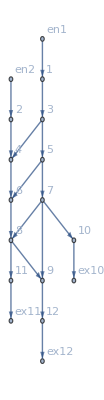

```mathematica
d2e["FG"]
```

```mathematica
Get[dddRicardo]
DataNoSplt=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{
{5,7,9,4001},{10,7,9,4001},{8,7,9,4001},
{11,8,9,4001},{6,8,9,4001},{7,8,9,4001}(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2eNoSplt=Data2Equations[DataNoSplt/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critNoSplt=CriticalCongestionSolver[d2eNoSplt];//AbsoluteTiming
```

It took 0.550657 seconds to preprocess.

Iterative DNF convertion took 11.335 seconds to terminate.

Reducing took 0.012232 seconds to terminate.

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{12.0132,Null}

```mathematica
IsNonLinearSolution[critNoSplt][critNoSplt["AssoCritical"]]
```

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-1.13687×10^-12,-1.13687×10^-12,0.,-1.13687×10^-12,-1.13687×10^-12,0.,-1.13687×10^-12,-1.13687×10^-12,0.,0.,-1.13687×10^-12,0.,-1.13687×10^-12,0.}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-12

<|u1→4000.,u2→3000.,u3→4000.,u4→3000.,u5→3000.,u6→3000.,u7→3000.,u8→2000.,u9→3000.,u10→2000.,u11→2000.,u12→2000.,u13→2000.,u14→1000.,u15→2000.,u16→1000.,u17→1000.,u18→1000.,u19→-2974.,u20→-2974.,u21→1000.,u22→0.,u23→-2974.,u24→-2974.,u25→1000.,u26→0.,u27→-2974.,u28→-2974.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→4000.,u36→4000.,u37→4000.,u38→4000.,j1→0.,j2→1000.,j3→0.,j4→1000.,j5→0.,j6→0.,j7→0.,j8→1000.,j9→0.,j10→1000.,j11→0.,j12→0.,j13→0.,j14→1000.,j15→0.,j16→1000.,j17→0.,j18→0.,j19→0.,j20→0.,j21→0.,j22→1000.,j23→0.,j24→0.,j25→0.,j26→1000.,j27→0.,j28→0.,j29→0.,j30→1000.,j31→0.,j32→1000.,j33→0.,j34→0.,j35→0.,j36→1000.,j37→0.,j38→1000.,jt1→0.,jt2→1000.,jt3→0.,jt4→1000.,jt5→0.,jt6→1000.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1000.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→1000.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→1000.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→0.,jt31→1000.,jt32→0.,jt33→0.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→0.,jt42→0.,jt43→1000.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→0.,jt55→0.,jt56→0.,jt57→0.,jt58→0.,jt59→1000.,jt60→0.,jt61→1000.,jt62→0.,jt63→0.,jt64→0.|>

```mathematica
{B,K,cost,vars}=GetKirchhoffMatrix[critNoSplt];
```

```mathematica
cost[vars]
```

{j1 j2+Abs[-j1+j2],j1 j2+Abs[-j1+j2],j3 j4+Abs[-j3+j4],j3 j4+Abs[-j3+j4],j5 j6+Abs[-j5+j6],j5 j6+Abs[-j5+j6],j7 j8+Abs[-j7+j8],j7 j8+Abs[-j7+j8],j10 j9+Abs[j10-j9],j10 j9+Abs[j10-j9],j11 j12+Abs[-j11+j12],j11 j12+Abs[-j11+j12],j13 j14+Abs[-j13+j14],j13 j14+Abs[-j13+j14],j15 j16+Abs[-j15+j16],j15 j16+Abs[-j15+j16],j17 j18+Abs[-j17+j18],j17 j18+Abs[-j17+j18],j19 j20+Abs[-j19+j20],j19 j20+Abs[-j19+j20],j21 j22+Abs[-j21+j22],j21 j22+Abs[-j21+j22],j23 j24+Abs[-j23+j24],j23 j24+Abs[-j23+j24],j25 j26+Abs[-j25+j26],j25 j26+Abs[-j25+j26],j27 j28+Abs[-j27+j28],j27 j28+Abs[-j27+j28],0,0,0,0,0,1000000+jt1 jt2,jt1 jt2,1000000+jt3 jt4,jt3 jt4,jt5 jt7,jt6 jt9,jt5 jt7,jt10 jt8,jt6 jt9,jt10 jt8,jt11 jt13,jt12 jt15,jt11 jt13,jt14 jt16,jt12 jt15,jt14 jt16,jt17 jt19,jt18 jt21,jt17 jt19,jt20 jt22,jt18 jt21,jt20 jt22,jt23 jt25,jt24 jt27,jt23 jt25,jt26 jt28,jt24 jt27,jt26 jt28,jt29 jt32,4001+jt30 jt35,jt31 jt38,jt29 jt32,4001+jt33 jt36,jt34 jt39,jt30 jt35,jt33 jt36,jt37 jt40,jt31 jt38,jt34 jt39,4001+jt37 jt40,jt41 jt44,4001+jt42 jt47,jt43 jt50,jt41 jt44,4001+jt45 jt48,jt46 jt51,jt42 jt47,jt45 jt48,jt49 jt52,jt43 jt50,jt46 jt51,4001+jt49 jt52,jt53 jt55,jt54 jt57,jt53 jt55,jt56 jt58,jt54 jt57,jt56 jt58,jt59 jt60,1000000+jt59 jt60,jt61 jt62,1000000+jt61 jt62,jt63 jt64,1000000+jt63 jt64}

```mathematica
Clear[cost]
```

```mathematica
jvars=critNoSplt["jvars"];
jtvars=critNoSplt["jtvars"];
CostArgs2 = critNoSplt["CostArgs2"]
```

<|{1,1->3}→Abs[j1]+Abs[j2],{3,1->3}→Abs[j1]+Abs[j2],{2,2->4}→Abs[j3]+Abs[j4],{4,2->4}→Abs[j3]+Abs[j4],{3,3->4}→Abs[j5]+Abs[j6],{4,3->4}→Abs[j5]+Abs[j6],{3,3->5}→Abs[j7]+Abs[j8],{5,3->5}→Abs[j7]+Abs[j8],{4,4->6}→Abs[j10]+Abs[j9],{6,4->6}→Abs[j10]+Abs[j9],{5,5->6}→Abs[j11]+Abs[j12],{6,5->6}→Abs[j11]+Abs[j12],{5,5->7}→Abs[j13]+Abs[j14],{7,5->7}→Abs[j13]+Abs[j14],{6,6->8}→Abs[j15]+Abs[j16],{8,6->8}→Abs[j15]+Abs[j16],{7,7->8}→Abs[j17]+Abs[j18],{8,7->8}→Abs[j17]+Abs[j18],{7,7->9}→Abs[j19]+Abs[j20],{9,7->9}→Abs[j19]+Abs[j20],{7,7->10}→Abs[j21]+Abs[j22],{10,7->10}→Abs[j21]+Abs[j22],{8,8->9}→Abs[j23]+Abs[j24],{9,8->9}→Abs[j23]+Abs[j24],{8,8->11}→Abs[j25]+Abs[j26],{11,8->11}→Abs[j25]+Abs[j26],{9,9->12}→Abs[j27]+Abs[j28],{12,9->12}→Abs[j27]+Abs[j28],{10,10->ex10}→Abs[j29]+Abs[j30],{ex10,10->ex10}→0,{11,11->ex11}→Abs[j31]+Abs[j32],{ex11,11->ex11}→0,{12,12->ex12}→Abs[j33]+Abs[j34],{ex12,12->ex12}→0,{en1,en1->1}→Abs[j35]+Abs[j36],{1,en1->1}→0,{en2,en2->2}→Abs[j37]+Abs[j38],{2,en2->2}→0,{1,1->3,en1->1}→1000000+Abs[jt1]+Abs[jt2],{1,en1->1,1->3}→Abs[jt1]+Abs[jt2],{2,2->4,en2->2}→1000000+Abs[jt3]+Abs[jt4],{2,en2->2,2->4}→Abs[jt3]+Abs[jt4],{3,1->3,3->4}→Abs[jt5]+Abs[jt7],{3,1->3,3->5}→Abs[jt6]+Abs[jt9],{3,3->4,1->3}→Abs[jt5]+Abs[jt7],{3,3->4,3->5}→Abs[jt10]+Abs[jt8],{3,3->5,1->3}→Abs[jt6]+Abs[jt9],{3,3->5,3->4}→Abs[jt10]+Abs[jt8],{4,2->4,3->4}→Abs[jt11]+Abs[jt13],{4,2->4,4->6}→Abs[jt12]+Abs[jt15],{4,3->4,2->4}→Abs[jt11]+Abs[jt13],{4,3->4,4->6}→Abs[jt14]+Abs[jt16],{4,4->6,2->4}→Abs[jt12]+Abs[jt15],{4,4->6,3->4}→Abs[jt14]+Abs[jt16],{5,3->5,5->6}→Abs[jt17]+Abs[jt19],{5,3->5,5->7}→Abs[jt18]+Abs[jt21],{5,5->6,3->5}→Abs[jt17]+Abs[jt19],{5,5->6,5->7}→Abs[jt20]+Abs[jt22],{5,5->7,3->5}→Abs[jt18]+Abs[jt21],{5,5->7,5->6}→Abs[jt20]+Abs[jt22],{6,4->6,5->6}→Abs[jt23]+Abs[jt25],{6,4->6,6->8}→Abs[jt24]+Abs[jt27],{6,5->6,4->6}→Abs[jt23]+Abs[jt25],{6,5->6,6->8}→Abs[jt26]+Abs[jt28],{6,6->8,4->6}→Abs[jt24]+Abs[jt27],{6,6->8,5->6}→Abs[jt26]+Abs[jt28],{7,5->7,7->8}→Abs[jt29]+Abs[jt32],{7,5->7,7->9}→4001+Abs[jt30]+Abs[jt35],{7,5->7,7->10}→Abs[jt31]+Abs[jt38],{7,7->8,5->7}→Abs[jt29]+Abs[jt32],{7,7->8,7->9}→4001+Abs[jt33]+Abs[jt36],{7,7->8,7->10}→Abs[jt34]+Abs[jt39],{7,7->9,5->7}→Abs[jt30]+Abs[jt35],{7,7->9,7->8}→Abs[jt33]+Abs[jt36],{7,7->9,7->10}→Abs[jt37]+Abs[jt40],{7,7->10,5->7}→Abs[jt31]+Abs[jt38],{7,7->10,7->8}→Abs[jt34]+Abs[jt39],{7,7->10,7->9}→4001+Abs[jt37]+Abs[jt40],{8,6->8,7->8}→Abs[jt41]+Abs[jt44],{8,6->8,8->9}→4001+Abs[jt42]+Abs[jt47],{8,6->8,8->11}→Abs[jt43]+Abs[jt50],{8,7->8,6->8}→Abs[jt41]+Abs[jt44],{8,7->8,8->9}→4001+Abs[jt45]+Abs[jt48],{8,7->8,8->11}→Abs[jt46]+Abs[jt51],{8,8->9,6->8}→Abs[jt42]+Abs[jt47],{8,8->9,7->8}→Abs[jt45]+Abs[jt48],{8,8->9,8->11}→Abs[jt49]+Abs[jt52],{8,8->11,6->8}→Abs[jt43]+Abs[jt50],{8,8->11,7->8}→Abs[jt46]+Abs[jt51],{8,8->11,8->9}→4001+Abs[jt49]+Abs[jt52],{9,7->9,8->9}→Abs[jt53]+Abs[jt55],{9,7->9,9->12}→Abs[jt54]+Abs[jt57],{9,8->9,7->9}→Abs[jt53]+Abs[jt55],{9,8->9,9->12}→Abs[jt56]+Abs[jt58],{9,9->12,7->9}→Abs[jt54]+Abs[jt57],{9,9->12,8->9}→Abs[jt56]+Abs[jt58],{10,7->10,10->ex10}→Abs[jt59]+Abs[jt60],{10,10->ex10,7->10}→1000000+Abs[jt59]+Abs[jt60],{11,8->11,11->ex11}→Abs[jt61]+Abs[jt62],{11,11->ex11,8->11}→1000000+Abs[jt61]+Abs[jt62],{12,9->12,12->ex12}→Abs[jt63]+Abs[jt64],{12,12->ex12,9->12}→1000000+Abs[jt63]+Abs[jt64]|>

```mathematica
cost=AssociationThread[vars,KeyMap[Join[jvars,jtvars]][CostArgs2]/@vars];
CCost=cost/@vars/. MapThread[Rule,{vars,#}]&;
```

KeyMap::invak: The argument CostArgs2 is not a valid Association.

KeyMap::invak: The argument j1 is not a valid Association.

KeyMap::invak: The argument j2 is not a valid Association.

General::stop: Further output of KeyMap::invak will be suppressed during this calculation.

Iterative DNF convertion...

Iterative DNF convertion took 30.846 seconds to terminate. 
Removing duplicates and reducing...

Iterative DNF convertion...

Iterative DNF convertion took 7.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

Iterative DNF convertion...

Iterative DNF convertion took 4.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

Iterative DNF convertion...

Iterative DNF convertion took 4.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{31.9327,Null}

Iterative DNF convertion took 31.9716 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{33.0927,Null}

Iterative DNF convertion took 32.1124 seconds to terminate

Iterative DNF convertion took 0.106322 seconds to terminate

Iterative DNF convertion took 0.015021 seconds to terminate

Iterative DNF convertion took 0.010981 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{33.4,Null}

Iterative DNF convertion took 32.4519 seconds to terminate

Iterative DNF convertion took 0.119409 seconds to terminate

Iterative DNF convertion took 0.016928 seconds to terminate

Iterative DNF convertion took 0.012381 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{33.8057,Null}

Iterative DNF convertion took 32.7087 seconds to terminate

Iterative DNF convertion took 0.11252 seconds to terminate

Iterative DNF convertion took 0.015535 seconds to terminate

Iterative DNF convertion took 0.011943 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{33.931,Null}

{34.2689,Null}

Iterative DNF convertion took 69.4619 seconds to terminate

Iterative DNF convertion took 0.47554 seconds to terminate

Iterative DNF convertion took 0.012635 seconds to terminate

Iterative DNF convertion took 0.016156 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001≤u19≤0

Picked one value for the variable(s) {u19} {-2974} (respectively)

{71.1561,Null}

Iterative DNF convertion took 68.8192 seconds to terminate

Iterative DNF convertion took 0.56005 seconds to terminate

Iterative DNF convertion took 0.015319 seconds to terminate

Iterative DNF convertion took 0.014922 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001≤u19≤0

Picked one value for the variable(s) {u19} {-2974} (respectively)

{70.7355,Null}

```mathematica
Get[dddRicardo]
DataNoSplt=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{
{5,7,9,4001},{10,7,9,4001},{8,7,9,4001},
{11,8,9,4001},{6,8,9,4001},{7,8,9,4001}(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2eNoSplt=Data2Equations[DataNoSplt/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
{B,K,cost,vars}=GetKirchhoffMatrix[d2eNoSplt];
```

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

It took 0.782012 seconds to preprocess.

Iterative DNF convertion took 4.85955 seconds to terminate.

Reducing took 0.007351 seconds to terminate.

{5.81805,Null}

Iterative DNF convertion took 4.84015 seconds to terminate

Iterative DNF convertion took 0.097742 seconds to terminate

Iterative DNF convertion took 0.007525 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{5.81485,Null}

Iterative DNF convertion took 5.27945 seconds to terminate

Iterative DNF convertion took 0.074018 seconds to terminate

Iterative DNF convertion took 0.003639 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{5.96865,Null}

Iterative DNF convertion took 34.4623 seconds to terminate

Iterative DNF convertion took 0.188789 seconds to terminate

Iterative DNF convertion took 0.003909 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{35.4993,Null}

Iterative DNF convertion took 23.213 seconds to terminate

Iterative DNF convertion took 0.185029 seconds to terminate

Iterative DNF convertion took 0.005296 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{24.3659,Null}

```mathematica
IsNonLinearSolution[critSplt][critSplt["AssoCritical"]]
```

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-1.13687×10^-12,-1.13687×10^-12,0.,-1.13687×10^-12,-1.13687×10^-12,0.,-1.13687×10^-12,-1.13687×10^-12,0.,-2.84217×10^-13,-7.95808×10^-13,-2.84217×10^-13,-7.95808×10^-13,-5.68434×10^-13}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-12

<|u1→3750.,u2→2750.,u3→3750.,u4→2750.,u5→2750.,u6→2750.,u7→2750.,u8→1750.,u9→2750.,u10→1750.,u11→1750.,u12→1750.,u13→1750.,u14→750.,u15→1750.,u16→750.,u17→750.,u18→750.,u19→750.,u20→500.,u21→750.,u22→0.,u23→750.,u24→500.,u25→750.,u26→0.,u27→500.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→3750.,u36→3750.,u37→3750.,u38→3750.,j1→0.,j2→1000.,j3→0.,j4→1000.,j5→0.,j6→0.,j7→0.,j8→1000.,j9→0.,j10→1000.,j11→0.,j12→0.,j13→0.,j14→1000.,j15→0.,j16→1000.,j17→0.,j18→0.,j19→0.,j20→250.,j21→0.,j22→750.,j23→0.,j24→250.,j25→0.,j26→750.,j27→0.,j28→500.,j29→0.,j30→750.,j31→0.,j32→750.,j33→0.,j34→500.,j35→0.,j36→1000.,j37→0.,j38→1000.,jt1→0.,jt2→1000.,jt3→0.,jt4→1000.,jt5→0.,jt6→1000.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1000.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→1000.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→1000.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→250.,jt31→750.,jt32→0.,jt33→0.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→0.,jt42→250.,jt43→750.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→250.,jt55→0.,jt56→250.,jt57→0.,jt58→0.,jt59→750.,jt60→0.,jt61→750.,jt62→0.,jt63→500.,jt64→0.|>

```mathematica
Get[dddRicardo]
(*this has large but not infinity costs on entrance and exits*)
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

It took 0.592909 seconds to preprocess.

Iterative DNF convertion took 3.61849 seconds to terminate.

Reducing took 0.00606 seconds to terminate.

{4.34646,Null}

Iterative DNF convertion...

... took 4.62555 seconds to terminate. 
Removing duplicates and reducing...

... took 0.005882 seconds to terminate.

Iterative DNF convertion...

... took 5.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000059 seconds to terminate.

{5.46973,Null}

{5.48268,Null}

Iterative DNF convertion took 4.76683 seconds to terminate

Iterative DNF convertion took 0.096058 seconds to terminate

Iterative DNF convertion took 0.007089 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{5.79336,Null}

```mathematica
??ZAnd
```

```mathematica
??ZAnd
```

Iterative DNF convertion took 5.45181 seconds to terminate

Iterative DNF convertion took 0.16761 seconds to terminate

Iterative DNF convertion took 0.008081 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

{6.22325,Null}

## Tigran

# Example 21

```mathematica
Get[dddRicardo]

ClearAll[H]
ClearAll[GG]
ClearAll[GG1]
RoundValues[x_?NumberQ]:=Round[x,10^-10];
NumberVectorQ[j_]:=And@@(NumberQ/@j);
H[j_?NumberVectorQ]:=DiagonalMatrix[1/#&/@j];
H2[j_?NumberVectorQ]:=DiagonalMatrix[1/#^2&/@j];
H42[j_?NumberVectorQ]:=DiagonalMatrix[1/#^4&/@j];
H3[j_?NumberVectorQ]:=DiagonalMatrix[1/#^(1/4)&/@j];
H4[j_?NumberVectorQ]:=DiagonalMatrix[1/#^(1/16)&/@j];
H5[j_?NumberVectorQ,t_]:=DiagonalMatrix[1/#^(1/(16+t))&/@j];
InvH[j_?NumberVectorQ]:=DiagonalMatrix[j];
NumberMatrixQ[A_]:=NumberVectorQ@Flatten@A;
AHA[x_?NumberVectorQ,A_, At_]:=A  .H3[x].At;
InvAHA[x_?NumberVectorQ,A_, At_]:=A  .InvH[x].At;
GG::usage = 
"GG[x,A,dim,At] is a good matrix.";
GG[x_?NumberVectorQ,A_, dim_, At_]:=Module[{MM,num},
MM=InvAHA[x,A,At];
num=LinearAlgebra`Private`MatrixConditionNumber[MM];
If[num>2.9*10^7,
ConstantArray[0,{dim,dim}],
InvH[x].(IdentityMatrix[dim]-At.Inverse[InvAHA[x,A,At] ] .A . InvH[x] )]
];
GG1[x_?NumberVectorQ,A_, dim_, At_,y_?NumberVectorQ]:=Module[{MM,diagonal,num,yy,gg,gg1},
MM=InvAHA[x,A,At];
yy=H[Diagonal[InvAHA[y,K,At]]];
gg=InvH[x].(IdentityMatrix[dim]-At.Inverse[InvAHA[x,A,At] ] .A . InvH[x] );
gg1=InvH[x].(IdentityMatrix[dim]-At.Inverse[yy.MM ].yy .A . InvH[x] );
(*invyy=DiagonalMatrix[1/#&/@y];*)
num=LinearAlgebra`Private`MatrixConditionNumber[MM];
If[num<2 10^6,
Return[gg],
Return[gg1]]
];
GG2[x_?NumberVectorQ,A_, dim_, At_,y_?NumberVectorQ]:=Module[{MM,diagonal,yy,gg1,num,cc,yt},
MM=InvAHA[x,A,At];
yt=y;
yy=H[Diagonal[InvAHA[yt,K,At]]];
num=LinearAlgebra`Private`MatrixConditionNumber[yy.MM];
cc=ConstantArray[0,{dim,dim}];
If[num>3*10^7,
cc,
InvH[x].(IdentityMatrix[dim]-At.Inverse[yy.MM ].yy .A . InvH[x])]
(*invyy=DiagonalMatrix[1/#&/@y];*)
];
GG3[x_?NumberVectorQ,A_, dim_, At_,y_?NumberVectorQ]:=Module[{MM,diagonal,yy,gg1,num,m0},
MM=Rationalize[InvAHA[x,A,At],10^-7];
yy=H[Diagonal[InvAHA[y,A,At]]];
(*yy=yt^(t+10);*)
num=LinearAlgebra`Private`MatrixConditionNumber[yy.MM];
m0=ConstantArray[0,{dim,dim}];
If[num>5*10^7,
m0,
InvH[x].(IdentityMatrix[dim]-At.Inverse[yy.MM ].yy .A . InvH[x])]
(*invyy=DiagonalMatrix[1/#&/@y];*)
];

GG4[x_?NumberVectorQ,A_, dim_, At_,y_?NumberVectorQ]:=Module[{MM,UPMM,LOMM,yy,DI,num,InvDI,PRE0,m0},
MM=InvAHA[x,A,At];
UPMM=UpperTriangularize[MM,1];
LOMM=LowerTriangularize[MM,-1];
DI=DiagonalMatrix[Diagonal[MM]];
InvDI=H2[Diagonal[MM]+1];
PRE0=DI+LOMM;
yy=Inverse[PRE0];
num=LinearAlgebra`Private`MatrixConditionNumber[yy.MM];
m0=ConstantArray[0,{dim,dim}];
If[num>4*10^7,
m0,
InvH[x].(IdentityMatrix[dim]-At.Inverse[yy.MM ].yy .A . InvH[x])]
(*invyy=DiagonalMatrix[1/#&/@y];*)
];

GG5[x_?NumberVectorQ,A_, dim_, At_,y_?NumberVectorQ]:=Module[{MM,UPMM,LOMM,yy,DI,num,InvDI,PRE0,m0},
MM=InvAHA[x,A,At];
UPMM=UpperTriangularize[MM,1];
LOMM=LowerTriangularize[MM,-1];
DI=DiagonalMatrix[Diagonal[MM]];
InvDI=H[Diagonal[MM]];
PRE0=(DI+LOMM ).InvDI.(DI+UPMM);
yy=Inverse[PRE0];
num=LinearAlgebra`Private`MatrixConditionNumber[MM.yy];
m0=ConstantArray[0,{dim,dim}];
If[num>4*10^7,
m0,
InvH[x].(IdentityMatrix[dim]-At.yy.Inverse[MM.yy ] .A . InvH[x])]
(*invyy=DiagonalMatrix[1/#&/@y];*)
];
GG6[x_?NumberVectorQ,A_, dim_, At_]:=Module[{MM,UPMM,LOMM,yyr,yyl,DI,num,InvDI,PRE0,m0,L},
MM=InvAHA[x,A,At];
UPMM=UpperTriangularize[MM,1];
LOMM=LowerTriangularize[MM,-1];
DI=DiagonalMatrix[Diagonal[MM]];
InvDI=H[Diagonal[MM]];
PRE0=(DI+LOMM ).InvDI.(DI+UPMM);
L=Transpose[CholeskyDecomposition[PRE0]];
yyl=Inverse[L];
yyr=Transpose[yyl];
num=LinearAlgebra`Private`MatrixConditionNumber[yyl.MM.yyr];
m0=ConstantArray[0,{dim,dim}];
If[num>4*10^7,
InvH[x].(IdentityMatrix[dim]-At.yyr.Inverse[yyl.MM.yyr ] .yyl.A . InvH[x]),
InvH[x].(IdentityMatrix[dim]-At.yyr.Inverse[yyl.MM.yyr ] .yyl.A . InvH[x])]
(*invyy=DiagonalMatrix[1/#&/@y];*)
];

PreC[x_?NumberVectorQ,A_, dim_, At_]:=Module[{MM,UPMM,LOMM,yy,DI,num,InvDI,PRE0,m0},
MM=InvAHA[x,A,At];
UPMM=UpperTriangularize[MM,1];
LOMM=LowerTriangularize[MM,-1];
DI=DiagonalMatrix[Diagonal[MM]];
InvDI=H[Diagonal[MM]];
PRE0=(DI+LOMM ).InvDI.(DI+UPMM);
yy=Inverse[PRE0]
];
```

```mathematica
GG6[]
```

```mathematica
(Diagonal[MM4])-(Diagonal[MM4])^2
```

```mathematica
MM4=InvAHA[x2,K,At];
MM04=InvAHA[xx[[1]],K,At];
UPMM4=UpperTriangularize[MM04,1];
LOMM4=LowerTriangularize[MM04,-1];
DI4=DiagonalMatrix[(Diagonal[MM04])];
InDI4=DiagonalMatrix[(Diagonal[MM04])^2];
UPMM=UpperTriangularize[MM4,1];
LOMM=LowerTriangularize[MM4,-1];
DI=DiagonalMatrix[(Diagonal[MM4])];
InDI=DiagonalMatrix[(Diagonal[MM4])^2];
PRE40=DI4+LOMM4;
PRE401=DI4+UPMM4;
PRE41=InDI4+4LOMM;
PRE0=DI+LOMM;
PRE01=DI+UPMM;
PRE1=InDI+LOMM;
yy401=Inverse[PRE401];
yy41=Inverse[PRE41];
yy4=Inverse[PRE40];
yy01=Inverse[PRE01];
yy1=Inverse[PRE1];
yy=Inverse[PRE0];
LinearAlgebra`Private`MatrixConditionNumber[yy4.MM4]
LinearAlgebra`Private`MatrixConditionNumber[yy41.MM4]
LinearAlgebra`Private`MatrixConditionNumber[yy401.MM4]
LinearAlgebra`Private`MatrixConditionNumber[yy.MM4.yy4]
LinearAlgebra`Private`MatrixConditionNumber[yy1.MM4]
LinearAlgebra`Private`MatrixConditionNumber[yy01.MM4]
```

7.90528×10^9

2.43933×10^12

7.39676×10^9

4.18251×10^9

3.63021×10^14

4.00001×10^7

```mathematica
InvAHA[x2,K,At]//MatrixForm;
```

```mathematica
GG6[x2,K,dim,At]
```

{{1.72005×10^-16,1.72005×10^-16,3.77712×10^-52,-2.19594×10^-33,1.76899×10^-34,-1.76899×10^-34,7.97278×10^-51,-4.63521×10^-32,2.38792×10^-52,-1.38829×10^-33,2.29862×10^-35,-2.29862×10^-35,74,-3.49116×10^-35,5.77654×10^-36,-4.76301×10^-36,3.49116×10^-35,4.76301×10^-36,-5.1028×10^-32,-7.01908×10^-57,2.69663×10^-34,3.70931×10^-59,-2.3629×10^-41,-2.60356×10^-57},95,{1}}
 |  |  |  |

```mathematica
MM7=Rationalize[InvAHA[x2,K,At],10^-7];
yy=H[Diagonal[InvAHA[x2,K,At]]];
(*yy=yt^(t+10);*)
num=LinearAlgebra`Private`MatrixConditionNumber[yy.MM]
```

∞

```mathematica
mn=0.91;
MM=InvAHA[x2,K,At];
UPMM=UpperTriangularize[MM,1];
LOMM=LowerTriangularize[MM,-1];
DI=DiagonalMatrix[Diagonal[MM]];
InvDI=DiagonalMatrix[(Diagonal[MM])^2];
PRE0=(DI+LOMM/mn)/mn;
Pre=Inverse[PRE0];
num=LinearAlgebra`Private`MatrixConditionNumber[Pre.MM]
```

3.97792×10^7

```mathematica
x2s=Sign[x2]*Max[x2];
```

```mathematica
x2=xx[[2]]
```

{1.72005×10^-16,1000.,1.72005×10^-16,1000.,0.982455,0.982455,1.72005×10^-16,1000.,1.72005×10^-16,1000.,0.982455,0.982455,1.72005×10^-16,1000.,1.72005×10^-16,1000.,0.982455,0.982455,4.57596,4.57596,3.50326×10^-16,1000.,4.57596,4.57596,3.50326×10^-16,1000.,3.97675,3.97675,1000.,1000.,1.61677×10^-6,1000.,1000.,-1.32856×10^-22,1000.,-1.32856×10^-22,1000.,2.42061,998.005,0.39875,2.42061,0.0270552,0.39875,2.42061,998.005,0.39875,2.42061,0.0270552,0.39875,2.42061,998.005,0.39875,2.42061,0.0270552,0.39875,2.42061,998.005,0.39875,2.42061,0.0270552,0.39875,2.42061,1.05891×10^-8,998.005,0.39875,4.30409×10^-9,2.42061,-2.03239×10^-26,-2.71251×10^-26,-2.10556×10^-26,0.0270552,0.39875,7.99518×10^-7,2.42061,1.05891×10^-8,998.005,0.39875,4.30409×10^-9,2.42061,-2.03239×10^-26,-2.7125×10^-26,-2.10556×10^-26,0.0270552,0.39875,7.99518×10^-7,0.982455,5.12757,0.982455,5.12757,5.12757,5.12757,1000.,-1.37553×10^-22,1000.,-1.37554×10^-22,1.61443×10^-6,-1.77886×10^-22}

```mathematica
x2
```

{3998.01,3998.01,3998.01,3998.01,1.,1.,3998.01,3998.01,3998.01,3998.01,1.,1.,3998.01,3998.01,3998.01,3998.01,1.,1.,946.43,527312.,3047.5,-523318.,946.43,527312.,3047.5,-523318.,2942.33,1.05567×10^6,-526365.,-526365.,1.05273×10^6,0.,0.,1.001×10^6,1.001×10^6,1.001×10^6,1.001×10^6,-498.003,2997.01,500.003,-498.003,1999.01,500.003,-498.003,2997.01,500.003,-498.003,1999.01,500.003,-498.003,2997.01,500.003,-498.003,1999.01,500.003,-498.003,2997.01,500.003,-498.003,1999.01,500.003,-1299.87,-410.505,10417.3,1301.87,890.361,311.273,5413.5,4112.64,4922.41,1991.59,-309.273,540334.,-1299.87,-410.505,10417.3,1301.87,890.361,311.273,5413.5,4112.64,4922.41,1991.59,-309.273,540334.,1.,526315.,1.,526315.,-50.5776,-50.5776,473693.,1.00006×10^6,473693.,1.00006×10^6,2.05268×10^6,999947.}

```mathematica
MM=InvAHA[x0,K,At];
yt=x0+ crrm[x0];
yy=H4[Diagonal[InvAHA[yt,K,At]]];
zz=H5[Diagonal[InvAHA[x0,K,At]],2];
num=LinearAlgebra`Private`MatrixConditionNumber[yy.MM]
LinearAlgebra`Private`MatrixConditionNumber[zz.MM]
```

1993.43

1109.02

```mathematica
x2=GG2[x0,K,dim,At,x0].cc[x0]//N
```

```mathematica
x0
```

```mathematica
Diagonal[MM7]+1
```

{1.,1.,2.01×10^6,2.002×10^6,2.01×10^6,2.002×10^6,12995.,7.,12995.,12995.,7.,12995.,12995.,7.,12995.,12995.,7.,12995.,25410.9,5010.,1.08352×10^6,37398.,25410.9,5010.,1.08352×10^6,37398.,1.05452×10^6,1.05452×10^6,2.11114×10^6,953483.,947388.,953483.,947388.,4.11124×10^6,4.10536×10^6}

```mathematica
mn=1;
MM7=
(*InvAHA[x2,K,At];*)
Rationalize[InvAHA[x2,K,At],10^-7]//N;
UPMM=UpperTriangularize[MM7,1];
LOMM=LowerTriangularize[MM7,-1];
DI=DiagonalMatrix[Diagonal[MM7]];
InvDI=H[(Diagonal[MM7])];
PRE07=(DI+LOMM *mn).InvDI.(DI+mn*UPMM)*(1/(mn(2-mn)));
Pre=Inverse[PRE07];
L=Transpose[CholeskyDecomposition[PRE07]];
Linv=Inverse[L];
LTinve=Inverse[Transpose[L]];
LinearAlgebra`Private`MatrixConditionNumber[Pre.MM7]
LinearAlgebra`Private`MatrixConditionNumber[Linv.MM7.LTinve]
```

2.65233×10^7

2.29108×10^7

```mathematica
x2
```

```mathematica
MMn=InvAHA[x2,K,At];
MM5=InvAHA[x2,K,At];
UPMM=UpperTriangularize[MM5,1];
LOMM=LowerTriangularize[MM5,-1];
DI=DiagonalMatrix[Diagonal[MM5]+1];
PRE01=DI+LOMM;
yy=Inverse[PRE01];
num=LinearAlgebra`Private`MatrixConditionNumber[yy.MM5]
```

∞

```mathematica
L=Transpose[CholeskyDecomposition[MM2]];
```

```mathematica
MM2-L.Transpose[L];
```

```mathematica
x2
```

```mathematica
x2=xx[[2]];
```

```mathematica
MM2=InvAHA[x2,K,At];
yt=Abs[x2]+ Abs[cc[x2]]+1;
yy=H3[Diagonal[InvAHA[yt,K,At]]];
zz=H5[Diagonal[InvAHA[x2,K,At]],1];
LinearAlgebra`Private`MatrixConditionNumber[yy.MM2]
LinearAlgebra`Private`MatrixConditionNumber[zz.MM2]
```

1.64294×10^10

7.62213×10^9

```mathematica
x2=GG3[x0,K,dim,At,x0]. crrm[x0];
```

```mathematica
Clear[Data,d2e,B,K,cost,jj,cc,x00,yy,sol,xx];
(*Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/D2E2.m"]*)
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{
  {5, 7, 9, 5001}, {10, 7, 9, 5001}, {8, 7, 9, 5001},
  {11, 8, 9, 5001}, {6, 8, 9, 5001}, {7, 8, 9, 5001}(*{12,9,7,
  1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,
  1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,
  7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,
  3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,
  s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,
  12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}
|>;
d2e = Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0, U3->0}];
(alg=CriticalCongestionSolver[d2e]);//AbsoluteTiming
algsol=alg["AssoCritical"];
```

It took 0.678755 seconds to preprocess.

Iterative DNF convertion took 13.2296 seconds to terminate.

Reducing took 0.012708 seconds to terminate.

MFGSS: Multiple solutions: -4001.≤u19≤0.

Picked one value for the variable(s) {u19} {-3974.} (respectively)

{14.0605,Null}

```mathematica
d2e["FG"]
```

-Graphics-

```mathematica
d2e["jvars"]
```

<|{1,1->3}→j1,{3,1->3}→j2,{2,2->4}→j3,{4,2->4}→j4,{3,3->4}→j5,{4,3->4}→j6,{3,3->5}→j7,{5,3->5}→j8,{4,4->6}→j9,{6,4->6}→j10,{5,5->6}→j11,{6,5->6}→j12,{5,5->7}→j13,{7,5->7}→j14,{6,6->8}→j15,{8,6->8}→j16,{7,7->8}→j17,{8,7->8}→j18,{7,7->9}→j19,{9,7->9}→j20,{7,7->10}→j21,{10,7->10}→j22,{8,8->9}→j23,{9,8->9}→j24,{8,8->11}→j25,{11,8->11}→j26,{9,9->12}→j27,{12,9->12}→j28,{10,10->ex10}→j29,{ex10,10->ex10}→j30,{11,11->ex11}→j31,{ex11,11->ex11}→j32,{12,12->ex12}→j33,{ex12,12->ex12}→j34,{en1,en1->1}→j35,{1,en1->1}→j36,{en2,en2->2}→j37,{2,en2->2}→j38|>

```mathematica
d2e["jtvars"]
```

<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->4,en2->2}→jt3,{2,en2->2,2->4}→jt4,{3,1->3,3->4}→jt5,{3,1->3,3->5}→jt6,{3,3->4,1->3}→jt7,{3,3->4,3->5}→jt8,{3,3->5,1->3}→jt9,{3,3->5,3->4}→jt10,{4,2->4,3->4}→jt11,{4,2->4,4->6}→jt12,{4,3->4,2->4}→jt13,{4,3->4,4->6}→jt14,{4,4->6,2->4}→jt15,{4,4->6,3->4}→jt16,{5,3->5,5->6}→jt17,{5,3->5,5->7}→jt18,{5,5->6,3->5}→jt19,{5,5->6,5->7}→jt20,{5,5->7,3->5}→jt21,{5,5->7,5->6}→jt22,{6,4->6,5->6}→jt23,{6,4->6,6->8}→jt24,{6,5->6,4->6}→jt25,{6,5->6,6->8}→jt26,{6,6->8,4->6}→jt27,{6,6->8,5->6}→jt28,{7,5->7,7->8}→jt29,{7,5->7,7->9}→jt30,{7,5->7,7->10}→jt31,{7,7->8,5->7}→jt32,{7,7->8,7->9}→jt33,{7,7->8,7->10}→jt34,{7,7->9,5->7}→jt35,{7,7->9,7->8}→jt36,{7,7->9,7->10}→jt37,{7,7->10,5->7}→jt38,{7,7->10,7->8}→jt39,{7,7->10,7->9}→jt40,{8,6->8,7->8}→jt41,{8,6->8,8->9}→jt42,{8,6->8,8->11}→jt43,{8,7->8,6->8}→jt44,{8,7->8,8->9}→jt45,{8,7->8,8->11}→jt46,{8,8->9,6->8}→jt47,{8,8->9,7->8}→jt48,{8,8->9,8->11}→jt49,{8,8->11,6->8}→jt50,{8,8->11,7->8}→jt51,{8,8->11,8->9}→jt52,{9,7->9,8->9}→jt53,{9,7->9,9->12}→jt54,{9,8->9,7->9}→jt55,{9,8->9,9->12}→jt56,{9,9->12,7->9}→jt57,{9,9->12,8->9}→jt58,{10,7->10,10->ex10}→jt59,{10,10->ex10,7->10}→jt60,{11,8->11,11->ex11}→jt61,{11,11->ex11,8->11}→jt62,{12,9->12,12->ex12}→jt63,{12,12->ex12,9->12}→jt64|>

```mathematica
AssociationThread[jj,(jj/.assol3)]
```

```mathematica
AssociationThread[jj,x2000//RoundValues//N]
```

```mathematica
(*checks the correction of function crr*)
```

```mathematica
jjE={j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26,j27,j28,j29,j30,j31,j32,j33,j34,j35,j36,j37,j38};
```

```mathematica
AssociationThread[{j4,j10,j16,jt42,j26},{j4,j10,j16,jt42,j26}/.AssociationThread[jj,
(jj/.algsol)]]
```

<|j4→1000,j10→1000,j16→1000,jt42→0,j26→1000|>

```mathematica
AssociationThread[{j2,j8,j14,j22,j20,j19,j28,j27,j34},{j2,j8,j14,j22,j20,j19,j28,j27,j34}/.AssociationThread[jj,(jj/.algsol)]]
```

```mathematica
<|j2->1000,j8->1000,j14->1000,j22->1000,j20->0,j19->0,j28->0,j27->0,j34->0|>
```

<|j2→1000,j8→1000,j14→1000,j22→1000,j20→0,j19→0,j28→0,j27→0,j34→0|>

```mathematica
AssociationThread[{j2,j8,j14,j22,j20,j19,j28,j27,j34},{j2,j8,j14,j22,j20,j19,j28,j27,j34}/.AssociationThread[jj,(jj/.assol4)]]
```

<|j2→1000.,j8→1000.,j14→1000.,j22→1000.,j20→4.53551,j19→4.53551,j28→3.95012,j27→3.95012,j34→9.19079×10^-7|>

```mathematica
AssociationThread[{j4,j10,j16,j26,j25,j32},{j4,j10,j16,j26,j25,j32}/.AssociationThread[jj,(jj/.assol4)]]//N
```

<|j4→1000.,j10→1000.,j16→1000.,j26→1000.,j25→1.64398×10^-16,j32→1000.|>

```mathematica
AssociationThread[{j4,j10,j16,j26,j25,j32},{j4,j10,j16,j26,j25,j32}/.AssociationThread[jj,(jj/.algsol)]]
```

<|j4→1000,j10→1000,j16→1000,j26→1000,j25→0,j32→1000|>

```mathematica
AssociationThread[{j2,j8,j14,j22,j20,j19,j28,j27,j34},{j2,j8,j14,j22,j20,j19,j28,j27,j34}/.AssociationThread[jj,
cost[jj]]]
```

<|j2→j1 j2+Abs[-j1+j2],j8→j7 j8+Abs[-j7+j8],j14→j13 j14+Abs[-j13+j14],j22→j21 j22+Abs[-j21+j22],j20→j19 j20+Abs[-j19+j20],j19→j19 j20+Abs[-j19+j20],j28→j27 j28+Abs[-j27+j28],j27→j27 j28+Abs[-j27+j28],j34→0|>

```mathematica
AssociationThread[{j2,j8,j14,j22,j20,j19,j28,j27,j34},{j2,j8,j14,j22,j20,j19,j28,j27,j34}/.AssociationThread[jj,
cc[Range[97]]]]
```

<|j2→3,j8→57,j14→183,j22→463,j20→381,j19→381,j28→757,j27→757,j34→0|>

```mathematica
{B,K,cost,jj}=GetKirchhoffMatrix[d2e];
(cc[j_?NumberVectorQ]:= cost[j])//Quiet
```

```mathematica
cc[Range[Length[vars]]]
```

{3000001/1000000,3000001/1000000,7000001/1000000,7000001/1000000,11000001/1000000,11000001/1000000,15000001/1000000,15000001/1000000,19000001/1000000,19000001/1000000,23000001/1000000,23000001/1000000,27000001/1000000,27000001/1000000,31000001/1000000,31000001/1000000,35000001/1000000,35000001/1000000,39000001/1000000,39000001/1000000,43000001/1000000,43000001/1000000,47000001/1000000,47000001/1000000,51000001/1000000,51000001/1000000,55000001/1000000,55000001/1000000,0,0,0,0,0,1000069,69,1000073,73,78,81,78,84,81,84,90,93,90,96,93,96,102,105,102,108,105,108,114,117,114,120,117,120,127,5132,135,127,5136,139,131,135,143,135,139,5144,151,5156,159,151,5160,163,155,159,167,159,163,5168,174,177,174,180,177,180,185,1000185,189,1000189,193,1000193}

```mathematica
cost[vars]
```

{1/1000000+Abs[j1]+Abs[j2],1/1000000+Abs[j1]+Abs[j2],1/1000000+Abs[j3]+Abs[j4],1/1000000+Abs[j3]+Abs[j4],1/1000000+Abs[j5]+Abs[j6],1/1000000+Abs[j5]+Abs[j6],1/1000000+Abs[j7]+Abs[j8],1/1000000+Abs[j7]+Abs[j8],1/1000000+Abs[j10]+Abs[j9],1/1000000+Abs[j10]+Abs[j9],1/1000000+Abs[j11]+Abs[j12],1/1000000+Abs[j11]+Abs[j12],1/1000000+Abs[j13]+Abs[j14],1/1000000+Abs[j13]+Abs[j14],1/1000000+Abs[j15]+Abs[j16],1/1000000+Abs[j15]+Abs[j16],1/1000000+Abs[j17]+Abs[j18],1/1000000+Abs[j17]+Abs[j18],1/1000000+Abs[j19]+Abs[j20],1/1000000+Abs[j19]+Abs[j20],1/1000000+Abs[j21]+Abs[j22],1/1000000+Abs[j21]+Abs[j22],1/1000000+Abs[j23]+Abs[j24],1/1000000+Abs[j23]+Abs[j24],1/1000000+Abs[j25]+Abs[j26],1/1000000+Abs[j25]+Abs[j26],1/1000000+Abs[j27]+Abs[j28],1/1000000+Abs[j27]+Abs[j28],0,0,0,0,0,1000000+Abs[jt1]+Abs[jt2],Abs[jt1]+Abs[jt2],1000000+Abs[jt3]+Abs[jt4],Abs[jt3]+Abs[jt4],Abs[jt5]+Abs[jt7],Abs[jt6]+Abs[jt9],Abs[jt5]+Abs[jt7],Abs[jt10]+Abs[jt8],Abs[jt6]+Abs[jt9],Abs[jt10]+Abs[jt8],Abs[jt11]+Abs[jt13],Abs[jt12]+Abs[jt15],Abs[jt11]+Abs[jt13],Abs[jt14]+Abs[jt16],Abs[jt12]+Abs[jt15],Abs[jt14]+Abs[jt16],Abs[jt17]+Abs[jt19],Abs[jt18]+Abs[jt21],Abs[jt17]+Abs[jt19],Abs[jt20]+Abs[jt22],Abs[jt18]+Abs[jt21],Abs[jt20]+Abs[jt22],Abs[jt23]+Abs[jt25],Abs[jt24]+Abs[jt27],Abs[jt23]+Abs[jt25],Abs[jt26]+Abs[jt28],Abs[jt24]+Abs[jt27],Abs[jt26]+Abs[jt28],Abs[jt29]+Abs[jt32],5001+Abs[jt30]+Abs[jt35],Abs[jt31]+Abs[jt38],Abs[jt29]+Abs[jt32],5001+Abs[jt33]+Abs[jt36],Abs[jt34]+Abs[jt39],Abs[jt30]+Abs[jt35],Abs[jt33]+Abs[jt36],Abs[jt37]+Abs[jt40],Abs[jt31]+Abs[jt38],Abs[jt34]+Abs[jt39],5001+Abs[jt37]+Abs[jt40],Abs[jt41]+Abs[jt44],5001+Abs[jt42]+Abs[jt47],Abs[jt43]+Abs[jt50],Abs[jt41]+Abs[jt44],5001+Abs[jt45]+Abs[jt48],Abs[jt46]+Abs[jt51],Abs[jt42]+Abs[jt47],Abs[jt45]+Abs[jt48],Abs[jt49]+Abs[jt52],Abs[jt43]+Abs[jt50],Abs[jt46]+Abs[jt51],5001+Abs[jt49]+Abs[jt52],Abs[jt53]+Abs[jt55],Abs[jt54]+Abs[jt57],Abs[jt53]+Abs[jt55],Abs[jt56]+Abs[jt58],Abs[jt54]+Abs[jt57],Abs[jt56]+Abs[jt58],Abs[jt59]+Abs[jt60],1000000+Abs[jt59]+Abs[jt60],Abs[jt61]+Abs[jt62],1000000+Abs[jt61]+Abs[jt62],Abs[jt63]+Abs[jt64],1000000+Abs[jt63]+Abs[jt64]}

```mathematica
vars
```

{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26,j27,j28,j30,j32,j34,j36,j38,jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt60,jt61,jt62,jt63,jt64}

```mathematica
$Aborted
"n="4"->"5.206426578372343
"n="4"->"0.cost@vars
```

{Abs[j1]+Abs[j2],Abs[j1]+Abs[j2],Abs[j3]+Abs[j4],Abs[j3]+Abs[j4],Abs[j5]+Abs[j6],Abs[j5]+Abs[j6],Abs[j7]+Abs[j8],Abs[j7]+Abs[j8],Abs[j10]+Abs[j9],Abs[j10]+Abs[j9],Abs[j11]+Abs[j12],Abs[j11]+Abs[j12],Abs[j13]+Abs[j14],Abs[j13]+Abs[j14],Abs[j15]+Abs[j16],Abs[j15]+Abs[j16],Abs[j17]+Abs[j18],Abs[j17]+Abs[j18],Abs[j19]+Abs[j20],Abs[j19]+Abs[j20],Abs[j21]+Abs[j22],Abs[j21]+Abs[j22],Abs[j23]+Abs[j24],Abs[j23]+Abs[j24],Abs[j25]+Abs[j26],Abs[j25]+Abs[j26],Abs[j27]+Abs[j28],Abs[j27]+Abs[j28],0,0,0,0,0,1000000+Abs[jt1]+Abs[jt2],Abs[jt1]+Abs[jt2],1000000+Abs[jt3]+Abs[jt4],Abs[jt3]+Abs[jt4],Abs[jt5]+Abs[jt7],Abs[jt6]+Abs[jt9],Abs[jt5]+Abs[jt7],Abs[jt10]+Abs[jt8],Abs[jt6]+Abs[jt9],Abs[jt10]+Abs[jt8],Abs[jt11]+Abs[jt13],Abs[jt12]+Abs[jt15],Abs[jt11]+Abs[jt13],Abs[jt14]+Abs[jt16],Abs[jt12]+Abs[jt15],Abs[jt14]+Abs[jt16],Abs[jt17]+Abs[jt19],Abs[jt18]+Abs[jt21],Abs[jt17]+Abs[jt19],Abs[jt20]+Abs[jt22],Abs[jt18]+Abs[jt21],Abs[jt20]+Abs[jt22],Abs[jt23]+Abs[jt25],Abs[jt24]+Abs[jt27],Abs[jt23]+Abs[jt25],Abs[jt26]+Abs[jt28],Abs[jt24]+Abs[jt27],Abs[jt26]+Abs[jt28],Abs[jt29]+Abs[jt32],5001+Abs[jt30]+Abs[jt35],Abs[jt31]+Abs[jt38],Abs[jt29]+Abs[jt32],5001+Abs[jt33]+Abs[jt36],Abs[jt34]+Abs[jt39],Abs[jt30]+Abs[jt35],Abs[jt33]+Abs[jt36],Abs[jt37]+Abs[jt40],Abs[jt31]+Abs[jt38],Abs[jt34]+Abs[jt39],5001+Abs[jt37]+Abs[jt40],Abs[jt41]+Abs[jt44],5001+Abs[jt42]+Abs[jt47],Abs[jt43]+Abs[jt50],Abs[jt41]+Abs[jt44],5001+Abs[jt45]+Abs[jt48],Abs[jt46]+Abs[jt51],Abs[jt42]+Abs[jt47],Abs[jt45]+Abs[jt48],Abs[jt49]+Abs[jt52],Abs[jt43]+Abs[jt50],Abs[jt46]+Abs[jt51],5001+Abs[jt49]+Abs[jt52],Abs[jt53]+Abs[jt55],Abs[jt54]+Abs[jt57],Abs[jt53]+Abs[jt55],Abs[jt56]+Abs[jt58],Abs[jt54]+Abs[jt57],Abs[jt56]+Abs[jt58],Abs[jt59]+Abs[jt60],1000000+Abs[jt59]+Abs[jt60],Abs[jt61]+Abs[jt62],1000000+Abs[jt61]+Abs[jt62],Abs[jt63]+Abs[jt64],1000000+Abs[jt63]+Abs[jt64]}

```mathematica
jj/.AssociationThread[jj,jj/.AssociationThread[jj,
cc[Range[97]]]]
```

{3,3,7,7,11,11,15,15,19,19,23,23,27,27,31,31,35,35,39,39,43,43,47,47,51,51,55,55,0,0,0,0,0,1000069,69,1000073,73,78,81,78,84,81,84,90,93,90,96,93,96,102,105,102,108,105,108,114,117,114,120,117,120,127,5132,135,127,5136,139,131,135,143,135,139,5144,151,5156,159,151,5160,163,155,159,167,159,163,5168,174,177,174,180,177,180,185,1000185,189,1000189,193,1000193}

```mathematica
x0={1,1001,1,1001,1,1,1,1001,1,1001,1,1,1,1001,1,1001,1,1,1,1001/2,1,1003/2,1,1001/2,1,1003/2,1,1000,1001/2,1001/2,999,1000,1000,1,1001,1,1001,1,1001,1,1,1,1,1,1001,1,1,1,1,1,1001,1,1,1,1,1,1001,1,1,1,1,1,1,1001,1,1,1,1,1,1,1,1,1001/2,1,1,1001,1,1,1,1,1,1,1,1,1001/2,1,1001/2,1,1001/2,1,1,1003/2,1,1003/2,1,1000,1};
dim = Length[x0];
At=Transpose[K];
```

```mathematica
(x0=(jj/.FindInstance[K.jj==B&&And@@((#>0)&/@jj),jj]//First);)//AbsoluteTiming
```

{11.8692,Null}

```mathematica
And@@Thread[GreaterEqual[#,0]&/@x0]
K.x0-B==(0&/@B)
```

True

True

```mathematica
cost[vars]
```

{Abs[j1]+Abs[j2],Abs[j1]+Abs[j2],Abs[j3]+Abs[j4],Abs[j3]+Abs[j4],Abs[j5]+Abs[j6],Abs[j5]+Abs[j6],Abs[j7]+Abs[j8],Abs[j7]+Abs[j8],Abs[j10]+Abs[j9],Abs[j10]+Abs[j9],Abs[j11]+Abs[j12],Abs[j11]+Abs[j12],Abs[j13]+Abs[j14],Abs[j13]+Abs[j14],Abs[j15]+Abs[j16],Abs[j15]+Abs[j16],Abs[j17]+Abs[j18],Abs[j17]+Abs[j18],Abs[j19]+Abs[j20],Abs[j19]+Abs[j20],Abs[j21]+Abs[j22],Abs[j21]+Abs[j22],Abs[j23]+Abs[j24],Abs[j23]+Abs[j24],Abs[j25]+Abs[j26],Abs[j25]+Abs[j26],Abs[j27]+Abs[j28],Abs[j27]+Abs[j28],0,0,0,0,0,1000000+Abs[jt1]+Abs[jt2],Abs[jt1]+Abs[jt2],1000000+Abs[jt3]+Abs[jt4],Abs[jt3]+Abs[jt4],Abs[jt5]+Abs[jt7],Abs[jt6]+Abs[jt9],Abs[jt5]+Abs[jt7],Abs[jt10]+Abs[jt8],Abs[jt6]+Abs[jt9],Abs[jt10]+Abs[jt8],Abs[jt11]+Abs[jt13],Abs[jt12]+Abs[jt15],Abs[jt11]+Abs[jt13],Abs[jt14]+Abs[jt16],Abs[jt12]+Abs[jt15],Abs[jt14]+Abs[jt16],Abs[jt17]+Abs[jt19],Abs[jt18]+Abs[jt21],Abs[jt17]+Abs[jt19],Abs[jt20]+Abs[jt22],Abs[jt18]+Abs[jt21],Abs[jt20]+Abs[jt22],Abs[jt23]+Abs[jt25],Abs[jt24]+Abs[jt27],Abs[jt23]+Abs[jt25],Abs[jt26]+Abs[jt28],Abs[jt24]+Abs[jt27],Abs[jt26]+Abs[jt28],Abs[jt29]+Abs[jt32],5001+Abs[jt30]+Abs[jt35],Abs[jt31]+Abs[jt38],Abs[jt29]+Abs[jt32],5001+Abs[jt33]+Abs[jt36],Abs[jt34]+Abs[jt39],Abs[jt30]+Abs[jt35],Abs[jt33]+Abs[jt36],Abs[jt37]+Abs[jt40],Abs[jt31]+Abs[jt38],Abs[jt34]+Abs[jt39],5001+Abs[jt37]+Abs[jt40],Abs[jt41]+Abs[jt44],5001+Abs[jt42]+Abs[jt47],Abs[jt43]+Abs[jt50],Abs[jt41]+Abs[jt44],5001+Abs[jt45]+Abs[jt48],Abs[jt46]+Abs[jt51],Abs[jt42]+Abs[jt47],Abs[jt45]+Abs[jt48],Abs[jt49]+Abs[jt52],Abs[jt43]+Abs[jt50],Abs[jt46]+Abs[jt51],5001+Abs[jt49]+Abs[jt52],Abs[jt53]+Abs[jt55],Abs[jt54]+Abs[jt57],Abs[jt53]+Abs[jt55],Abs[jt56]+Abs[jt58],Abs[jt54]+Abs[jt57],Abs[jt56]+Abs[jt58],Abs[jt59]+Abs[jt60],1000000+Abs[jt59]+Abs[jt60],Abs[jt61]+Abs[jt62],1000000+Abs[jt61]+Abs[jt62],Abs[jt63]+Abs[jt64],1000000+Abs[jt63]+Abs[jt64]}

```mathematica
che=CholeskyDecomposition[{{2,1},{1,2}}];
Transpose[che].che
```

{{2,1},{1,2}}

```mathematica
n=4;
dim = Length[x0];
At=Transpose[K];
(sol=NDSolve[x'[t]==-  GG6[x[t],K,dim,At].cc[x[t]]&&x[0]==x0,x[t],{t,0,n}, Method->"BDF"];)//AbsoluteTiming
xx=Table[x[t]/. sol[[1]],{t,0,n,1}];
x20003=xx[[n]];
assol4=AssociationThread[jj,xx[[n]]];
Print["n=",n,"->",Max[Abs[(jj/.algsol)-(jj/.assol4)]]]
Print["n=",n,"->",Max[Abs[xx[[n]]-xx[[n-1]]]]]
```

CholeskyDecomposition::posdef: The matrix {{1000.,0.,0.,1000.,0.,0.,0.,0.,0.,0.,«25»},{0.,1000.,0.,0.,0.,1000.,0.,0.,0.,0.,«25»},{0.,0.,2000.,-1000.,0.,0.,-1000.,0.,0.,0.,«25»},{1000.,0.,-1000.,3500.,0.,0.,500.,0.,0.,0.,«25»},«3»,{0.,0.,0.,0.,0.,0.,-333.315,724.045,-222.207,0.,«25»},{0.,0.,0.,0.,0.,0.,-666.685,-222.207,2388.43,0.,«25»},{0.,0.,0.,0.,-1000.,500.,0.,0.,0.,2500.,«25»},«25»} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

General::stop: Further output of CholeskyDecomposition::posdef will be suppressed during this calculation.

NDSolve::nlnum: The function value {-If[LinearAlgebra`Private`MatrixConditionNumber[Inverse[«1»].{«35»}.Transpose[«1»]]>40000000,InvH[{2.73783×10^-23,1000.,3.33041×10^-23,1000.,0.933,0.933,3.11452×10^-23,1000.,3.12163×10^-23,1000.,«87»}].(IdentityMatrix[97]-Dot[«6»]),InvH[{2.73783×10^-23,1000.,3.33041×10^-23,1000.,0.933,0.933,3.11452×10^-23,1000.,3.12163×10^-23,1000.,«87»}].(IdentityMatrix[97]-Dot[«6»])].{1000.,1000.,1000.,1000.,«4»,1000.,1000.,«87»}} is not a list of numbers with dimensions {97} at {t,x[t]} = {0.0359056,{2.73783×10^-23,1000.,3.33041×10^-23,1000.,0.933,0.933,3.11452×10^-23,1000.,3.12163×10^-23,1000.,«87»}}.

{13.8291,Null}

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

n=4->7.93789×10^6

n=4->5.6299×10^6

```mathematica
(vars/.algsol)+x0*10^-9
```

{1/1000000000,1000000001001/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1/1000000000,1/1000000000,1001/2000000000,1/1000000000,2000000001003/2000000000,1/1000000000,1001/2000000000,1/1000000000,2000000001003/2000000000,1/1000000000,1/1000000,2000000001001/2000000000,2000000001001/2000000000,999/1000000000,1000000001/1000000,1000000001/1000000,1/1000000000,1000000001001/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1001/2000000000,1/1000000000,1/1000000000,1000000001001/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1/1000000000,1001/2000000000,1/1000000000,1001/2000000000,1/1000000000,1001/2000000000,1/1000000000,1/1000000000,2000000001003/2000000000,1/1000000000,2000000001003/2000000000,1/1000000000,1/1000000,1/1000000000}

```mathematica
GG6[(vars/.algsol)+x0*10^-9,K,dim,At]
```

$Aborted

```mathematica
-  GG6[xx[[1]],K,dim,At].cc[xx[[1]]]
```

{-2002.,-2002.,-2002.,-2002.,-2.,-2.,-2002.,-2002.,-2002.,-2002.,-2.,-2.,-2002.,-2002.,-2002.,-2002.,-2.,-2.,-61.7614,-471090.,-1940.37,469088.,-61.7614,-471090.,-1940.37,469088.,-1058.88,-943115.,471028.,471028.,-942056.,-3.67169×10^-10,-3.67169×10^-10,-1.001×10^6,-1.001×10^6,-1.001×10^6,-1.001×10^6,497.501,-3000.01,-501.501,497.501,-2001.,-501.501,497.501,-3000.01,-501.501,497.501,-2001.,-501.501,497.501,-3000.01,-501.501,497.501,-2001.,-501.501,497.501,-3000.01,-501.501,497.501,-2001.,-501.501,1336.2,520.806,-10716.3,-1340.2,-817.394,-348.906,-5525.81,-4187.61,-5034.01,-1993.29,344.906,-485479.,1336.2,520.806,-10716.3,-1340.2,-817.394,-348.906,-5525.81,-4187.61,-5034.01,-1993.29,344.906,-485479.,-2.,-471090.,-2.,-471090.,-61.7614,-61.7614,-528922.,-999950.,-528922.,-999950.,-1.94212×10^6,-1.00006×10^6}

```mathematica
n=4;
dim = Length[x0];
At=Transpose[K];
(sol=NDSolve[x'[t]==-GG5[x[t],K,dim,At,x[t]].cc[x[t]]&&x[0]==x0,x[t],{t,0,n}, Method->"BDF"];)//AbsoluteTiming
xx=Table[x[t]/. sol[[1]],{t,0,n,1}];
x20003=xx[[n]];
assol4=AssociationThread[jj,xx[[n]]];
Print["n=",n,"->",Max[Abs[(jj/.algsol)-(jj/.assol4)]]]
Print["n=",n,"->",Max[Abs[xx[[n]]-xx[[n-1]]]]]
```

{16.7646,Null}

n=4->5.18892

n=4->1.77636×10^-15

```mathematica
Max[Abs[xx[[2]]-xx[[1]]]]
```

1000.

```mathematica
n=4;
dim = Length[x0];
At=Transpose[K];
(sol=NDSolve[x'[t]==-GG4[x[t],K,dim,At,x[t]].cc[x[t]]&&x[0]==x0,x[t],{t,0,n}, Method->"BDF"];)//AbsoluteTiming
xx=Table[x[t]/. sol[[1]],{t,0,n,1}];
x20003=xx[[n]];
assol4=AssociationThread[jj,xx[[n]]];
Print["n=",n,"->",Max[Abs[(jj/.algsol)-(jj/.assol4)]]]
Print["n=",n,"->",Max[Abs[xx[[n]]-xx[[n-1]]]]]
```

{19.6227,Null}

n=4->5.12757

n=4->1.87687×10^-9

```mathematica
Max[Abs[xx[[2]]-xx[[1]]]]
```

1000.

```mathematica
aa=xx;
```

```mathematica
Max[Abs[aa[[2]]-aa[[1]]]]
```

954.276

```mathematica
(*With complimentary conditions*)
```

```mathematica
n=64;
dim = Length[x0];
At=Transpose[K];
(sol=NDSolve[x'[t]==-GG3[x[t],K,dim,At,x[t]].crr[x[t]]&&x[0]==x0,x[t],{t,0,n}, Method->"BDF"];)//AbsoluteTiming
xx=Table[x[t]/. sol[[1]],{t,0,n,1}];
x20003=xx[[n]];
assol3=AssociationThread[jj,xx[[n]]];
Print["n=",n,"->",Max[Abs[(jj/.algsol)-(jj/.assol3)]]]
Print["n=",n,"->",Max[Abs[xx[[n]]-xx[[n-1]]]]]
```

{20.6007,Null}

n=64->470.724

n=64->7.96482×10^-9

{22.1263,Null}

n=8->473.397

n=8->4.4854×10^-7

{19.2172,Null}

n=2->495.943

n=2->995.943

{19.6971,Null}

n=128->496.807

n=128->0.

```mathematica
Clear[x]
```

```mathematica
(*Without complimentary conditions*)
```

```mathematica
n=128;
dim = Length[x0];
At=Transpose[K];
(sol=NDSolve[x'[t]==-GG2[x[t],K,dim,At,x[t]].crr[x[t]]&&x[0]==x0,x[t],{t,0,n}, Method->"BDF"];)//AbsoluteTiming
xx=Table[x[t]/. sol[[1]],{t,0,n,1}];
x2000=xx[[n]];
assol=AssociationThread[jj,xx[[n]]];
Print["n=",n,"->",Max[Abs[(jj/.algsol)-(jj/.assol)]]]
Print["n=",n,"->",Max[Abs[xx[[n]]-xx[[n-1]]]]]
```

{32.28,Null}

n=128->436.995

n=128->1.79156×10^-10

{42.2777,Null}

n=64->436.995

n=64->1.74188×10^-6

{35.7034,Null}

n=4->436.995

n=4->6.66875×10^-6

{45.2292,Null}

n=2->436.995

n=2->936.995

```mathematica
assol=AssociationThread[jj,x2000]
```

```mathematica
AssociationThread[jj,ccfm[x0]]
```

<|j1→2001.,j10→2001.,j11→1.,j12→1.,j13→2001.,j14→2001.,j15→2001.,j16→2001.,j17→1.,j18→1.,j19→1000.,j2→2001.,j20→1000.,j21→1002.,j22→1002.,j23→1000.,j24→1000.,j25→1002.,j26→1002.,j27→1999.,j28→1999.,j3→2001.,j30→500.5,j32→500.5,j34→999.,j36→1000.,j38→1000.,j4→2001.,j5→1.,j6→1.,j7→2001.,j8→2001.,j9→2001.,jt1→1.,jt10→1.,jt11→1.,jt12→1001.,jt13→1.,jt14→1.,jt15→1.,jt16→1.,jt17→1.,jt18→1001.,jt19→1.,jt2→1001.,jt20→1.,jt21→1.,jt22→1.,jt23→1.,jt24→1001.,jt25→1.,jt26→1.,jt27→1.,jt28→1.,jt29→1.,jt3→1.,jt30→1.,jt31→1001.,jt32→1.,jt33→1.,jt34→1.,jt35→1.,jt36→1.,jt37→1.,jt38→1.,jt39→1.,jt4→1001.,jt40→500.5,jt41→1.,jt42→1.,jt43→1001.,jt44→1.,jt45→1.,jt46→1.,jt47→1.,jt48→1.,jt49→1.,jt5→1.,jt50→1.,jt51→1.,jt52→500.5,jt53→1.,jt54→500.5,jt55→1.,jt56→500.5,jt57→1.,jt58→1.,jt59→501.5,jt6→1001.,jt60→1.,jt61→501.5,jt62→1.,jt63→1000.,jt64→1.,jt7→1.,jt8→1.,jt9→1.|>

```mathematica
assol
```

<|j1→-3.57003×10^-23,j10→1000.,j11→0.447209,j12→0.447214,j13→-3.71066×10^-21,j14→1000.,j15→-1.32511×10^-21,j16→1000.,j17→0.447214,j18→0.447214,j19→1.39096×10^-22,j2→1000.,j20→282.609,j21→-1.8237×10^-22,j22→717.391,j23→9.88361×10^-22,j24→282.609,j25→2.4645×10^-22,j26→717.391,j27→2.58034×10^-22,j28→565.217,j3→1.71686×10^-23,j30→717.391,j32→717.391,j34→565.217,j36→1000.,j38→1000.,j4→1000.,j5→0.447214,j6→0.447209,j7→-1.16179×10^-21,j8→1000.,j9→-2.985×10^-23,jt1→-3.70559×10^-27,jt10→-1.1553×10^-20,jt11→333.333,jt12→666.667,jt13→-1.15002×10^-20,jt14→333.333,jt15→1.25797×10^-24,jt16→-1.14317×10^-20,jt17→333.333,jt18→666.667,jt19→-1.27563×10^-20,jt2→1000.,jt20→333.333,jt21→1.26005×10^-24,jt22→-1.16593×10^-20,jt23→333.333,jt24→666.667,jt25→-1.14438×10^-20,jt26→333.333,jt27→1.258×10^-24,jt28→-1.13537×10^-20,jt29→250.,jt3→-2.5844×10^-27,jt30→320.652,jt31→429.348,jt32→-7.08666×10^-19,jt33→70.6522,jt34→179.348,jt35→-6.89349×10^-21,jt36→4.58904×10^-13,jt37→108.696,jt38→-4.25449×10^-22,jt39→-2.32591×10^-19,jt4→1000.,jt40→-1.15162×10^-12,jt41→250.,jt42→320.652,jt43→429.348,jt44→-7.0969×10^-19,jt45→70.6522,jt46→179.348,jt47→-6.44108×10^-21,jt48→4.58906×10^-13,jt49→108.696,jt5→333.333,jt50→-8.01447×10^-24,jt51→-2.32016×10^-19,jt52→-1.15163×10^-12,jt53→0.333333,jt54→282.609,jt55→0.333334,jt56→282.609,jt57→-2.55739×10^-18,jt58→-2.5574×10^-18,jt59→717.391,jt6→666.667,jt60→6.78077×10^-24,jt61→717.391,jt62→6.78075×10^-24,jt63→565.217,jt64→-1.29062×10^-22,jt7→-1.15155×10^-20,jt8→333.333,jt9→1.258×10^-24|>

```mathematica
Total[algsol]//N
```

80000.

```mathematica
jj
```

```mathematica
AssociationThread[jjE,(jjE/.algsol)-
(jjE/.assol)]//N
```

<|j1→3.57003×10^-23,j2→-3.12826×10^-6,j3→-1.71686×10^-23,j4→-0.0000117241,j5→-0.447214,j6→-0.447209,j7→1.16179×10^-21,j8→-3.30618×10^-6,j9→2.985×10^-23,j10→-0.0000196976,j11→-0.447209,j12→-0.447214,j13→3.71066×10^-21,j14→4.12637×10^-6,j15→1.32511×10^-21,j16→-1.4395×10^-6,j17→-0.447214,j18→-0.447214,j19→-1.39096×10^-22,j20→-32.6087,j21→1.8237×10^-22,j22→32.6087,j23→-9.88361×10^-22,j24→-32.6087,j25→-2.4645×10^-22,j26→32.6087,j27→-2.58034×10^-22,j28→-65.2174,j29→-1. j29,j30→32.6087,j31→-1. j31,j32→32.6087,j33→-1. j33,j34→-65.2174,j35→-1. j35,j36→0.,j37→-1. j37,j38→0.|>

```mathematica
{jt5,jt8,jt9}/.algsol
{jt5,jt8,jt9}/.assol
```

{0,0,0}

{333.333,333.333,9.84435×10^-25}

{292.468,Null}

n=16000->333.334

n=16000->0.0000133319

{202.675,Null}

n=8000->333.333

n=8000->5.91717×10^-7

{59.7191,Null}

n=4000->333.333

n=4000->1.40098×10^-6

{34.581,Null}

n=2000->333.333

n=2000->3.96856×10^-6

{19.0046,Null}

n=1000->333.333

n=1000->0.0000112175

{9.50069,Null}

n=500->333.333

n=500->0.0000317579

{7.6937,Null}

n=200->333.333

n=200->0.000126112

{5.68621,Null}

n=100->333.333

n=100->0.000358954

{9.31085,Null}

n=500->333.333

```mathematica
(*Without complimentary conditions*)
```

```mathematica
n=2;
dim = Length[x0];
At=Transpose[K];
(sol=NDSolve[x'[t]==-GG[x[t],K,dim,At].ccf[x[t]]&&x[0]==x0,x[t],{t,0,n}, Method->"BDF"];)//AbsoluteTiming
xx=Table[x[t]/. sol[[1]],{t,0,n,1}];
x2000=xx[[n]];
assol=AssociationThread[jj,xx[[n]]];
Print["n=",n,"->",Max[(jj/.algsol)-(jj/.assol)]]
```

{3.01756,Null}

n=2->333.333

```mathematica
n=1500;
dim = Length[x0];
At=Transpose[K];
(sol=NDSolve[x'[t]==-GG2[x[t],K,dim,At,x[t]].cmoo[x[t]]&&x[0]==x0,x[t],{t,0,n}, Method->"BDF"];)//AbsoluteTiming
xx=Table[x[t]/. sol[[1]],{t,0,n,1}];
x2000=xx[[n]];
assol=AssociationThread[jj,xx[[n]]];
Print["n=",n,"->",Max[(jj/.algsol)-(jj/.assol)]]
```

{88.6485,Null}

n=1500->333.333

{53.7822,Null}

n=1000->333.333

```mathematica
n=2000;
dim = Length[x0];
At=Transpose[K];
(sol=NDSolve[x'[t]==-GG2[x[t],K,dim,At,x[t]].cc[x[t]]&&x[0]==x0,x[t],{t,0,n}, Method->"BDF"];)//AbsoluteTiming
xx=Table[x[t]/. sol[[1]],{t,0,n,1}];
x2000=xx[[n]];
assol=AssociationThread[jj,xx[[n]]];
Print["n=",n,"->",Max[Abs[(jj/.algsol)-(jj/.assol)]]]
```

{17.9271,Null}

n=2000->0.0050434

{10.9759,Null}

n=1000->7.46502

{8.08443,Null}

n=500->195.868

## Test zone

```mathematica
gh[x_?NumberVectorQ,K_,dim_,At_,k_]:=Part[GG[x,K,dim,At].cc[x],k];
```

```mathematica
ghv[x_?NumberVectorQ,K_,dim_,At_]:=GG[x,K,dim,At].cc[x];
ghv[x0,K,dim,At];
```

```mathematica
FixedPoint[Function[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x60,x61,x62,x63,x64,x65,x66,x67,x68,x69,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x81,x82,x83,x84,x85,x86,x87,x88,x89,x90,x91,x92,x93,x94,x95,x96,x97},{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x60,x61,x62,x63,x64,x65,x66,x67,x68,x69,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x81,x82,x83,x84,x85,x86,x87,x88,x89,x90,x91,x92,x93,x94,x95,x96,x97}*5]@@#&,x0]
```

{{2},{3}}

```mathematica
With[{ϵ=0.2},FixedPoint[Function[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x60,x61,x62,x63,x64,x65,x66,x67,x68,x69,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x81,x82,x83,x84,x85,x86,x87,x88,x89,x90,x91,x92,x93,x94,x95,x96,x97},{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x60,x61,x62,x63,x64,x65,x66,x67,x68,x69,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x81,x82,x83,x84,x85,x86,x87,x88,x89,x90,x91,x92,x93,x94,x95,x96,x97}- ghv[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x60,x61,x62,x63,x64,x65,x66,x67,x68,x69,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x81,x82,x83,x84,x85,x86,x87,x88,x89,x90,x91,x92,x93,x94,x95,x96,x97},K,dim,At]]@@#&,x0]]
```

```mathematica
assol2=Table[With[{ϵ=0.0001},FixedPoint[Function[{x},{x- gh[x,K,dim,At,k]}]@@#&,x0[[k]]]],{k,1,dim}]
```

{1,1001,1,1,1,1001,1,1001,1,1,1,1001,1001/2,1,1003/2,1,1001/2,1,1003/2,1,1000,1,1001/2,1001/2,999,1000,1000,1001,1,1,1,1001,1,1,1,1,1001,1,1,1,1,1,1001,1,1001,1,1,1,1,1001,1,1,1,1,1,1,1,1001,1,1,1,1,1,1,1,1,1001,1001/2,1,1,1001,1,1,1,1,1,1,1,1,1,1001/2,1,1001/2,1,1001/2,1,1,1003/2,1001,1,1003/2,1,1000,1,1,1,1}

```mathematica
Length[assol2]
```

0

```mathematica
(jj/.algsol)
```

{0,1000,0,0,0,1000,0,1000,0,0,0,1000,250,0,750,0,250,0,750,0,500,0,750,750,500,1000,1000,1000,0,0,0,1000,0,0,0,0,1000,0,0,0,0,0,1000,0,1000,0,0,0,0,1000,0,0,0,0,0,0,250,750,0,0,0,0,0,0,0,0,1000,0,0,250,750,0,0,0,0,0,0,0,0,0,0,0,250,0,250,0,0,750,1000,0,750,0,500,0,0,0,0}

```mathematica
algsol
```

<|j36→1000,j38→1000,j35→0,j37→0,j29→0,j31→0,j33→0,j2→1000,j4→1000,j1→0,j6→0,j8→1000,j3→0,j5→0,j10→1000,j7→0,j12→0,j14→1000,j9→0,j11→0,j16→1000,j13→0,j18→0,j20→250,j22→750,j15→0,j17→0,j24→250,j26→750,j19→0,j23→0,j28→500,j21→0,j30→750,j25→0,j32→750,j27→0,j34→500,u30→0,u32→0,u34→0,jt12→1000,jt13→0,jt14→0,jt2→1000,jt20→0,jt23→0,jt24→1000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→1000,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→250,jt55→0,jt56→250,jt58→0,jt59→750,jt6→1000,jt60→0,jt61→750,jt62→0,jt63→500,jt64→0,jt7→0,jt8→0,jt9→0,u29→0,u31→0,u33→0,u36→3750,u38→3750,jt1→0,jt35→0,jt39→0,jt43→750,jt57→0,u10→1750,u13→1750,u14→750,u15→1750,u16→750,u17→750,u18→750,u2→2750,u20→500,u21→750,u22→0,u25→750,u26→0,u27→500,u28→0,u35→3750,u37→3750,u4→2750,u7→2750,u8→1750,u9→2750,jt15→0,jt21→0,jt47→0,jt18→1000,jt31→750,jt36→0,jt37→0,jt49→0,u1→3750,u11→1750,u12→1750,u19→750,u23→750,u24→500,u3→3750,u5→2750,u6→2750,jt10→0,jt11→0,jt16→0,jt17→0,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt30→250,jt32→0,jt33→0,jt34→0,jt41→0,jt42→250,jt44→0,jt45→0,jt48→0|>

```mathematica
Max[(jj/.algsol)-assol2]
```

499/2

```mathematica
With[{ϵ=0.1},FixedPoint[Function[x,{2 ϵ,0}+{{1-2 ϵ,0},{0,1-2 ϵ}}.x],x0]]
Function
```

$Aborted

```mathematica
jj
```

```mathematica
xx0={1,2,3};
```

```mathematica
aa=RecurrenceTable[{x[t+1]==x[t]-4x[t],x[0]==x0},x,{t,0,6}];
aa[[7]][[1]]
```

729

```mathematica
dim
```

97

```mathematica
Array[x,Length[dim]]
```

{}

```mathematica
x0
```

{2,1002,2,2,2,1002,2,1002,2,2,2,1002,1003/2,2,1005/2,2,1003/2,2,1005/2,2,1001,2,1003/2,1003/2,1000,1001,1001,1002,2,2,2,1002,2,2,2,2,1002,2,2,2,2,2,1002,2,1002,2,2,2,2,1002,2,2,2,2,2,2,2,1002,2,2,2,2,2,2,2,2,1002,1003/2,2,2,1002,2,2,2,2,2,2,2,2,2,1003/2,2,1003/2,2,1003/2,2,2,1005/2,1002,2,1005/2,2,1001,2,2,2,2}

```mathematica
With[{ϵ=0.1},FixedPoint[Function[x,{2 ϵ,0}+{{1-2 ϵ,0},{0,1-2 ϵ}}.x],x0]]
```

```mathematica
With[{ϵ=0.01},FixedPoint[Function[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x60,x61,x62,x63,x64,x65,x66,x67,x68,x69,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x81,x82,x83,x84,x85,x86,x87,x88,x89,x90,x91,x92,x93,x94,x95,x96,x97},{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x60,x61,x62,x63,x64,x65,x66,x67,x68,x69,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x81,x82,x83,x84,x85,x86,x87,x88,x89,x90,x91,x92,x93,x94,x95,x96,x97}+2 ϵ-2 {x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x43,x44,x45,x46,x47,x48,x49,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x60,x61,x62,x63,x64,x65,x66,x67,x68,x69,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x81,x82,x83,x84,x85,x86,x87,x88,x89,x90,x91,x92,x93,x94,x95,x96,x97} ϵ]@@#&,Table[40,dim]]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

### This is the NEW InvAHA: it makes the vector field vanish if the result is not invertible.

```mathematica
GG[x_?NumberVectorQ,A_, dim_, At_]:=Module[{MM},
MM=InvAHA[x,A,At];

If[Det[MM]==0.,
ConstantArray[0,{dim,dim}],
InvH[x].(IdentityMatrix[dim]-At.Inverse[InvAHA[x,A,At] ] .A . InvH[x] )]
];
```

```mathematica
{{1000.0000005508921,0.,0.,1000.0000005508921,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1000.,0.,0.,0.,1000.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.0652461529363658*^7,-33.8423747190368,0.,0.,1.0652495371738378*^7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1000.0000005508921,0.,-33.8423747190368,1033.8423752699289,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.0652461529363109*^7,-33.84237471812497,0.,0.,0.,1.0652495371737827*^7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1000.,0.,0.,-33.84237471812497,1033.842374718125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.0652495371738378*^7,0.,0.,0.,-1.0651491390584191*^7,-1.99460606593975,-1001.9865481196716,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-1.99460606593975,5.534512007979829,-1.994606065941541,0.,-1.5452998760985377,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-1001.9865481196716,-1.994606065941541,-1.0651491390580151*^7,0.,0.,0.,1.0652495371734338*^7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.0652495371737827*^7,0.,0.,0.,0.,-1.0651491390584283*^7,-1.994606064481478,-1001.986547480303,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-1.5452998760985377,0.,-1.994606064481478,5.534512005726853,-1.9946060651468378,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1001.986547480303,-1.9946060651468378,-1.0651491390586073*^7,0.,0.,0.,1.0652495371739617*^7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.0652495371734338*^7,0.,0.,0.,-1.0651491390598455*^7,-1.9946060652869768,-1001.9865298163237,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.9946060652869768,5.534512007170549,-1.9946060652421127,0.,-1.545299876641459,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1001.9865298163237,-1.9946060652421127,-1.0651491390596466*^7,0.,0.,0.,1.065249537173235*^7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.0652495371739617*^7,0.,0.,0.,-1.0651491390579745*^7,-1.994606065126854,-1001.9865538069422,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.545299876641459,0.,-1.994606065126854,5.534512007619892,-1.9946060658515785,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1001.9865538069422,-1.9946060658515785,-1.0651491390579825*^7,0.,0.,0.,0.,1.0652495371739699*^7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.065249537173235*^7,0.,0.,0.,6.029674421190396*^7,1.1073102271947823*^7,-1.062632796667596*^7,-7.139601388890818*^7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.1073102271947823*^7,8.773101663550214*^7,-2.932564820552379*^7,-6.94784691566263*^7,0.,-1.5452998779752238,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.062632796667596*^7,-2.932564820552379*^7,-1.1512953688255774*^12,5.739578101372565*^11,0.,0.,0.,0.,5.773775106644932*^11,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-7.139601388890818*^7,-6.94784691566263*^7,5.739578101372565*^11,-4.076494075503027*^10,0.,0.,0.,0.,0.,0.,0.,-5.3305199489918066*^11,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.0652495371739699*^7,0.,0.,0.,0.,6.02967442112546*^7,1.1073102271962004*^7,-1.0626327966625236*^7,-7.139601388833107*^7,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.5452998779752238,0.,0.,1.1073102271962004*^7,8.773101663547511*^7,-2.932564820551783*^7,-6.947846915661941*^7,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.0626327966625236*^7,-2.932564820551783*^7,-1.15129536882546*^12,5.739578101371908*^11,0.,5.773775106644415*^11,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-7.139601388833107*^7,-6.947846915661941*^7,5.739578101371908*^11,-4.076494075503314*^10,0.,0.,0.,0.,0.,-5.330519948991127*^11,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.773775106644932*^11,0.,0.,0.,0.,0.,-1.1516427330785686*^12,-1.9946048585328269,5.742652224160701*^11,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.773775106644415*^11,0.,-1.9946048585328269,-1.1516427330784658*^12,5.74265222416019*^11,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.742652224160701*^11,5.74265222416019*^11,-2.3101908702531523*^12,0.,0.,0.,0.,1.1616604254210632*^12,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-5.3305199489918066*^11,0.,0.,0.,0.,0.,0.,0.,1.1062914156124307*^12,-5.7323942071325*^11,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-5.7323942071325*^11,1.150305312528644*^12,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-5.330519948991127*^11,0.,0.,0.,0.,0.,1.1062914156123171*^12,-5.732394207132046*^11,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-5.732394207132046*^11,1.150305312528545*^12,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.1616604254210632*^12,0.,0.,0.,0.,-2.315270082022087*^12,1.1536096566010234*^12},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.1536096566010234*^12,-2.3077414382317676*^12}}//Det
```

6.10591×10^250

```mathematica
ln
```

```mathematica
x log(x)
```

```mathematica
suspect={{1000.0223291246112,0.,0.,1000.0223291246112,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,999.9951219859294,0.,0.,0.,999.9951219859294,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1999.975568712125,-999.9761880402175,0.,0.,-999.9993806719075,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1000.0223291246112,0.,-999.9761880402175,1999.9985171648286,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2000.052849391041,-1000.0004545832908,0.,0.,0.,-1000.0523948077504,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,999.9951219859294,0.,0.,-1000.0004545832908,1999.9955765692202,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-999.9993806719075,0.,0.,0.,1999.975760750292,-2.9230111725518045*^-7,-999.9763797860833,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-2.9230111725518045*^-7,0.0006871663676806184,-5.854164268777193*^-7,0.,-0.0006862886501364854,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-999.9763797860833,-5.854164268777193*^-7,1999.8942677884836,0.,0.,0.,-999.9178874169838,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1000.0523948077504,0.,0.,0.,0.,2000.003301761441,-6.190494352057322*^-7,-999.9509063346413,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-0.0006862886501364854,0.,-6.190494352057322*^-7,0.0006871309050933611,-2.2320552166993128*^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-999.9509063346413,-2.2320552166993128*^-7,1999.9567599909037,0.,0.,0.,-1000.0058534330569,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-999.9178874169838,0.,0.,0.,1999.9519387033647,-5.920669736549107*^-7,-1000.0340506943139,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-5.920669736549107*^-7,0.0006872402137921875,-3.886294894327645*^-7,0.,-0.0006862595173290999,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1000.0340506943139,-3.886294894327645*^-7,2000.0950415809766,0.,0.,0.,-1000.0609904980331,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1000.0058534330569,0.,0.,0.,2000.0018416795015,-4.1183217672439227*^-7,-999.9959878346123,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0006862595173290999,0.,-4.1183217672439227*^-7,0.0006872290093538456,-5.576598480213836*^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-999.9959878346123,-5.576598480213836*^-7,2000.0217092630533,0.,0.,0.,0.,-1000.0257208707812,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1000.0609904980331,0.,0.,0.,2000.0635389782815,-6.460273395676694*^-6,-249.97439703319543,-750.0281449867797,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-6.460273395676694*^-6,0.0007014378393908109,-8.6670559646751*^-6,-2.597732525379173*^-8,0.,-0.0006862845327052054,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-249.97439703319543,-8.6670559646751*^-6,499.9503116908848,-3.872115490474307*^-8,0.,0.,0.,0.,-249.97590595191224,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-750.0281449867797,-2.597732525379173*^-8,-3.872115490474307*^-8,1499.9910439954006,0.,0.,0.,0.,0.,0.,0.,-749.9628989439227,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1000.0257208707812,0.,0.,0.,0.,1999.9954521424493,-8.659402219969728*^-6,-249.99445780539182,-749.975264806874,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0006862845327052054,0.,0.,-8.659402219969728*^-6,0.0007014294305926048,-6.4661159470071966*^-6,-1.9379720422479595*^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-249.99445780539182,-6.4661159470071966*^-6,499.98773662386475,-3.8725475555065065*^-8,0.,-249.99327231363148,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-749.975264806874,-1.9379720422479595*^-8,-3.8725475555065065*^-8,1499.9555444319099,0.,0.,0.,0.,0.,-749.9802795669308,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-249.97590595191224,0.,0.,0.,0.,0.,499.9585629506653,-4.63774588727916*^-13,-249.98265699875256,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-249.99327231363148,0.,-4.63774588727916*^-13,499.98523391845436,-249.99196160482245,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-249.98265699875256,-249.99196160482245,999.9516284467227,0.,0.,0.,0.,-499.9770098431477,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-749.9628989439227,0.,0.,0.,0.,0.,0.,0.,1499.9401200713012,-749.9772211273785,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-749.9772211273785,1499.968443974862,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-749.9802795669308,0.,0.,0.,0.,0.,1499.9587918338448,-749.978512266914,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-749.978512266914,1499.956115634956,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-499.9770098431477,0.,0.,0.,0.,999.9541578347653,-499.9771479916175},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-499.9771479916175,999.951545847045}};
```

```mathematica
Dimensions[suspect]
```

{35,35}

```mathematica
dim
```

97

```mathematica
suspect[[35,35]]
```

999.952

```mathematica
diagonal=Table[Abs[suspect[[i,i]]],{i,1,35}];
```

{1000.02,999.995,1999.98,2000.,2000.05,2000.,1999.98,0.000687166,1999.89,2000.,0.000687131,1999.96,1999.95,0.00068724,2000.1,2000.,0.000687229,2000.02,2000.06,0.000701438,499.95,1499.99,2000.,0.000701429,499.988,1499.96,499.959,499.985,999.952,1499.94,1499.97,1499.96,1499.96,999.954,999.952}

```mathematica
Max@%/Min@%
```

2.91079×10^6

$Aborted

InterpolatingFunction::dmval: Input value {1575} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1576} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1577} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2.09265

{27.8362,Null}

n=4->31.6228

n=4->1.46835×10^-6

$Aborted

n=4->5.20643

n=4->0.

```mathematica
Get[dddRicardo]
```

```mathematica
{1,5,3,5,10,10,1}
```

```mathematica
Clear[keepSortedUnion]
```

```mathematica
keepSortedUnion[List[x_,xs__],v_]:=Append[DeleteCases[List@xs,v],v]
```

```mathematica
keepSortedUnion[{1,5,3,5,10,10,1},1]
```

{5,3,5,10,10,1}

```mathematica
keepSortedUnion[{5,3,5,10,10,1},5]
```

{3,10,10,1,5}

```mathematica
keepSortedUnion[{3,10,10,1,5},3]
```

{10,10,1,5,3}

```mathematica
keepSortedUnion[{10,10,1,5,3},5]
```

```mathematica
keepSortedUnion[{10,1,3,5},10]
```

```mathematica
keepSortedUnion[{1,3,5,10},10]
```

{3,5,10}

```mathematica
Fold[keepSortedUnion,{1,5,3,5,10,10,1},{1,5,3,5,10,10,1}]
```

{5,10,1}

```mathematica
first[List[x_,xs__]]:=xs
```

```mathematica
first[{34,3,3,4,4,5,2,2}]
```

Sequence[3,3,4,4,5,2,2]

```mathematica
DeleteCases[{1,5,3,5,10,10,1},]
```

{1,5,3,5,10,10,1}

```mathematica
??keepSortedUnion
```

```mathematica
RestoreOrder[subset_,list_]:=Last/@Sort[{Position[list,#,{1},1][[1,1]],#}&/@subset];
```

```mathematica
Reverse[Range[9]]
```

{9,8,7,6,5,4,3,2,1}

```mathematica
RestoreOrder[Range[4],Reverse[Range[9]]]
```

{4,3,2,1}

```mathematica
{Position[Reverse[Range[9]],#,{1},1],#}&/@Range[4]
```

{{{{9}},1},{{{8}},2},{{{7}},3},{{{6}},4}}